## Dilepton Case

### Load Parton Level (dσ̂/d Cθ)

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

(* Load dσ/dΩ *)

dσuu2lldCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-uu2ll_X-sec.txt"]];
dσdd2lldCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-dd2ll_X-sec.txt"]];
```

### PDF Convolution

```mathematica
SetDirectory["~/Google\ Drive/Research/Instruction/Tools/Cuba-4.2.1"];
Install["Vegas"];
```

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/math_package_v2";
SetDirectory[pdfpath];
<< NNPDF`
prefix=pdfpath<>"/Grids/";
namegrid = "NNPDF30_nlo_as_0118";
Timing[InitializePDFGrid[prefix,namegrid]]
```

Welcome in the Mathematica Package for NNPDF PDFs. The following Functions are available:

- Initializing and interpolating PDFs

InitializePDFGrid;

- Using NNPDF PDFs

xPDFcv; xPDFEnsemble; xPDFRep; xPDF; xPDFCL; xMin; xMax; Q2min; Q2Max; NumberPDF; HasPhoton;

- Parameters for the QCD analysis

alphaSMZ; mCharm; mBottom; mTop; MZ; alphas; Infoalphas; Lam4; Lam5;

For the usage of each of these Functions, please read the README file or type ?Function.

'Version' '5.8.8'

'Description:'

'NNPDF30_nlo_as_0118.LHgrid'

'Reference: arXiv:1410.8849'

'Fit: NLO global fit, alphas(MZ)=0.118'

'NNPDF Collaboration: R.D. Ball, V. Bertone, '

'S. Carrazza, C.S. Deans, L. Del Debbio, '

'S. Forte, A. Guffanti, N.P. Hartland, '

'J.I. Latorre, J. Rojo and M. Ubiali'

'This set has 100 member PDF'

'mem=0 --> average on replicas.'

'Evolution: pol. interpolation on the LH grid'

Grid division:

x axis: 100 points; 1.×10^-9 <= x <= 1.

Q^2 axis: 50 points; 1. <= Q^2 <= 1.×10^10

Reading PDF set from file. Please wait.

PDF set successfully read from file.

Interpolating PDF set on the grid. Please wait.

PDF grid interpolated. Ready to use the NNPDF set.

{13.4967,Null}

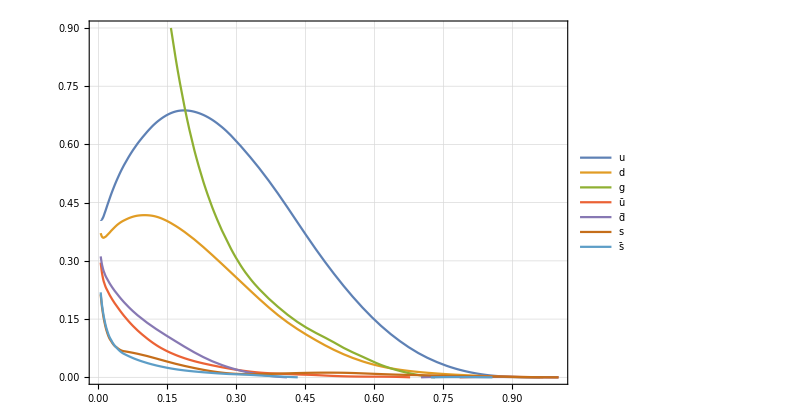

```mathematica
(* Plot xPDF : Peskin pg 563 *)
uppdf=xPDFcv[x,4,2];  (* Peak height is different from the Peskin *)
downpdf=xPDFcv[x,4,1];
gluepdf=xPDFcv[x,4,0];
upbarpdf=xPDFcv[x,4,-2];
dbarpdf=xPDFcv[x,4,-1];
spdf=xPDFcv[x,4,3];
sbarpdf=xPDFcv[x,4,-3];   
Plot[{uppdf,downpdf,gluepdf,upbarpdf,dbarpdf,spdf,sbarpdf},{x,0.005,1},PlotRange->{{0,1},{0,0.9}},PlotLegends->{"u","d","g","ū","d̄","s","s̄"}]
```

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;


(*pdf[x_,Q_,flav_]:=If[x≤1.0&&x>10^-9&&xPDFcv[x,Q^2,flav]>0,1/x xPDFcv[x,Q^2,flav],0]*)
pdf[x_,flav_]:=xPDFcv[x,mz^2,flav]/.mz->91.1876/.mw->80.387

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

uubarpdf=2/M(pdf[M/(√scoll)Exp[Y],2]pdf[M/(√scoll)Exp[-Y],-2]+pdf[M/(√scoll)Exp[Y],-2]pdf[M/(√scoll)Exp[-Y], 2]);
ddbarpdf=2/M(pdf[M/(√scoll)Exp[Y],1]pdf[M/(√scoll)Exp[-Y],-1]+pdf[M/(√scoll)Exp[Y],-1]pdf[M/(√scoll)Exp[-Y], 1]);
ccbarpdf=2/M(pdf[M/(√scoll)Exp[Y],4]pdf[M/(√scoll)Exp[-Y],-4]+pdf[M/(√scoll)Exp[Y],-4]pdf[M/(√scoll)Exp[-Y], 4]);
ssbarpdf=2/M(pdf[M/(√scoll)Exp[Y],3]pdf[M/(√scoll)Exp[-Y],-3]+pdf[M/(√scoll)Exp[Y],-3]pdf[M/(√scoll)Exp[-Y], 3]);
```

```mathematica
?xPDFcv
```

### Proton Level Calculation

#### dσ/dM Calculation

```mathematica
dσdCθuubar = dσuu2lldCθ;
dσdCθddbar = dσdd2lldCθ;
partonicσuubar[n_]:=Integrate[SeriesCoefficient[dσdCθuubar,{x,0,n}],{Cθ,-1,1}]/.{Ein->M/2}//Simplify
partonicσddbar[n_]:=Integrate[SeriesCoefficient[dσdCθddbar,{x,0,n}],{Cθ,-1,1}]/.{Ein->M/2}//Simplify
```

```mathematica
variablelistOx2uubar={δGF6^2, CHD6til δGF6, CHdc16til δGF6, CHec16til δGF6, CHL16til δGF6,CHL36til δGF6, CHQ16til δGF6,CHQ36til δGF6,CHuc16til δGF6,CHWB6til δGF6,CeQ6til δGF6,Ceu6til δGF6, CLQ36til δGF6, CLQ6til δGF6, CLu6til δGF6, CHD6til^2, CHD6til CHdc16til,CHD6til CHec16til,CHD6til CHL16til,CHD6til CHL36til, CHD6til CHQ16til,CHD6til CHQ36til,CHD6til CHuc16til,CHD6til CHWB6til,CeQ6til CHD6til,Ceu6til CHD6til,CHD6til CLQ36til,CHD6til CLQ6til,CHD6til CLu6til,CHdc16til^2, CHdc16til CHec16til, CHdc16til CHL16til,CHdc16til CHL36til,CHdc16til CHQ16til,CHdc16til CHQ36til, CHdc16til CHuc16til, CHdc16til CHWB6til, CeQ6til CHdc16til, Ceu6til CHdc16til, CHdc16til CLQ36til, CHdc16til CLQ6til, CHdc16til CLu6til, CHec16til^2, CHec16til CHL16til, CHec16til CHL36til, CHec16til CHQ16til, CHec16til CHQ36til, CHec16til CHuc16til, CHec16til CHWB6til, CeQ6til CHec16til, Ceu6til CHec16til, CHec16til CLQ36til, CHec16til CLQ6til, CHec16til CLu6til, CHL16til^2, CHL16til CHL36til, CHL16til CHQ16til, CHL16til CHQ36til, CHL16til CHuc16til, CHL16til CHWB6til, CeQ6til CHL16til, Ceu6til CHL16til, CHL16til CLQ36til, CHL16til CLQ6til, CHL16til CLu6til, CHL36til^2, CHL36til CHQ16til, CHL36til CHQ36til, CHL36til CHuc16til, CHL36til CHWB6til, CeQ6til CHL36til, Ceu6til CHL36til, CHL36til CLQ36til, CHL36til CLQ6til, CHL36til CLu6til, CHQ16til^2, CHQ16til CHQ36til, CHQ16til CHuc16til, CHQ16til CHWB6til, CeQ6til CHQ16til, Ceu6til CHQ16til, CHQ16til CLQ36til, CHQ16til CLQ6til, CHQ16til CLu6til, CHQ36til^2, CHQ36til CHuc16til, CHQ36til CHWB6til, CeQ6til CHQ36til, Ceu6til CHQ36til, CHQ36til CLQ36til, CHQ36til CLQ6til, CHQ36til CLu6til, CHuc16til^2, CHuc16til CHWB6til, CeQ6til CHuc16til, Ceu6til CHuc16til, CHuc16til CLQ36til, CHuc16til CLQ6til, CHuc16til CLu6til, CHWB6til^2, CeQ6til CHWB6til, Ceu6til CHWB6til, CHWB6til CLQ36til, CHWB6til CLQ6til, CHWB6til CLu6til, CHB6til CHWB6til, CHW6til CHWB6til, CeQ6til^2, Ceu6til^2, CLQ36til^2, CLQ36til CLQ6til, CLQ6til^2, CLu6til^2, δGF8, CHD28til, CHD8til, CHdc18til, CHec18til, CHL18til, CHL28til, CHL38til, CHQ18til, CHQ28til, CHQ38til,CHuc18til, CHW28til, CHWB8til, CeQs8til, CeQt8til, Ceus8til, Ceut8til, CHeQ18til, CHeQ38til, CHeu8til, CHLQ18til, CHLQ28til, CHLQ38til, CHLQ48til, CHLu18til, CHLu38til, CLQs18til, CLQs38til, CLQt18til, CLQt38til, CLus8til, CLut8til};

dσdMOx2uubarterm=Table[Coefficient[variableOx2uubar,variablelistOx2uubar[[wilson]]],{wilson,1,Length[variablelistOx2uubar]}];
```

```mathematica
variableSMuubar=partonicσuubar[0];
variableSMddbar=partonicσddbar[0];
variableOxuubar=partonicσuubar[1];
variableOxddbar=partonicσddbar[1];
variableOx2uubar=partonicσuubar[2];
variableOx2ddbar=partonicσddbar[2];
```

```mathematica
σpp2lνSMuu=1/10^5 Vegas[10^5 (variableSMuubar uubarpdf),{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
σpp2lνSMdd=1/10^5 Vegas[10^5 (variableSMddbar ddbarpdf),{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
```

Vegas::success: Needed 1000000 function evaluations.

(4.3703×10^6 | 2451.96 | 2.35815×10^-6)

Vegas::success: Needed 1000000 function evaluations.

(939609. | 546.465 | 1.15663×10^-6)

```mathematica
σpp2lνSMss=1/10^5 Vegas[10^5 (variableSMuubar ccbarpdf),{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
σpp2lνSMcc=1/10^5 Vegas[10^5 (variableSMddbar ssbarpdf),{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]
```

Vegas::success: Needed 1000000 function evaluations.

(2.06729×10^6 | 1178.87 | 2.60136×10^-7)

Vegas::success: Needed 1000000 function evaluations.

(662512. | 430.492 | 3.19694×10^-7)

```mathematica
variablelistOxuubar = DeleteDuplicates@Cases[variableOxuubar//N,_Symbol,Infinity]
variablelistOxuubar=Delete[variablelistOxuubar,{{1}}]
dσdMOxuubarterm=Table[Coefficient[variableOxuubar,variablelistOxuubar[[wilson]]],{wilson,1,Length[variablelistOxuubar]}];

variablelistOxddbar = DeleteDuplicates@Cases[variableOxddbar//N,_Symbol,Infinity]
variablelistOxddbar=Delete[variablelistOxddbar,{{1}}]
dσdMOxddbarterm=Table[Coefficient[variableOxddbar,variablelistOxddbar[[wilson]]],{wilson,1,Length[variablelistOxddbar]}];
```

{M,δGF6,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,CeQ6til,Ceu6til,CLQ36til,CLQ6til,CLu6til}

{δGF6,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,CeQ6til,Ceu6til,CLQ36til,CLQ6til,CLu6til}

{M,δGF6,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,Ced6til,CeQ6til,CLd6til,CLQ36til,CLQ6til}

{δGF6,CHD6til,CHdc16til,CHec16til,CHL16til,CHL36til,CHQ16til,CHQ36til,CHuc16til,CHWB6til,Ced6til,CeQ6til,CLd6til,CLQ36til,CLQ6til}

```mathematica
σpp2lνOxuubar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOxuubarterm[[i]]uubarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOxuubar,{ variablelistOxuubar[[i]],protonσ}],{i,1,Length[variablelistOxuubar]}],i];
σpp2lνOxuubar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

(δGF6 | (-1.2361×10^7 | 6889.92 | 2.35634×10^-6)
CHD6til | (-1.52394×10^7 | 8355.04 | 2.35541×10^-6)
CHdc16til | (115.496 | 0.056969 | 1.19887×10^-7)
CHec16til | (-1789.2 | 1.69616 | 7.69622×10^-9)
CHL16til | (722.009 | 0.69044 | 1.11022×10^-20)
CHL36til | (203.536 | 0.557496 | 8.77076×10^-20)
CHQ16til | (-1621.04 | 1.45073 | 1.2245×10^-9)
CHQ36til | (296.621 | 0.296573 | 0.)
CHuc16til | (704.393 | 0.653705 | 5.82393×10^-9)
CHWB6til | (-3.26416×10^7 | 17898.9 | 2.35538×10^-6)
CeQ6til | (-1939.23 | 1.25181 | 4.20242×10^-8)
Ceu6til | (-1940.34 | 1.13144 | 4.24941×10^-8)
CLQ36til | (1940.97 | 1.33372 | 4.31262×10^-8)
CLQ6til | (-1940.97 | 1.33372 | 4.31262×10^-8)
CLu6til | (-1939.59 | 1.11251 | 4.0888×10^-8))

```mathematica
σpp2lνOxddbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOxddbarterm[[i]]ddbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOxddbar,{ variablelistOxddbar[[i]],protonσ}],{i,1,Length[variablelistOxddbar]}],i];
σpp2lνOxddbar
```

Vegas::success: Needed 1000000 function evaluations.

Vegas::success: Needed 700000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

(δGF6 | (-2.65788×10^6 | 1635.81 | 1.07576×10^-6)
CHD6til | (-3.27662×10^6 | 1825.71 | 1.05963×10^-6)
CHdc16til | (-216.666 | 0.194903 | 4.25549×10^-9)
CHec16til | (-1510.57 | 1.425 | 3.27556×10^-9)
CHL16til | (835.354 | 0.784433 | 1.00312×10^-16)
CHL36til | (351.437 | 0.469332 | 2.22045×10^-21)
CHQ16til | (986.279 | 0.960525 | 6.39923×10^-9)
CHQ36til | (306.006 | 0.292624 | 3.9188×10^-19)
CHuc16til | (-143.739 | 0.0710003 | 7.73389×10^-8)
CHWB6til | (-7.01732×10^6 | 3915.18 | 1.06055×10^-6)
Ced6til | (814.534 | 0.46428 | 1.52232×10^-8)
CeQ6til | (816.825 | 0.686526 | 1.43808×10^-8)
CLd6til | (815.301 | 0.471122 | 1.52283×10^-8)
CLQ36til | (812.406 | 0.701972 | 1.56546×10^-8)
CLQ6til | (812.406 | 0.701972 | 1.56546×10^-8))

```mathematica
σpp2lνOxccbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOxuubarterm[[i]]ccbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOxccbar,{ variablelistOxuubar[[i]],protonσ}],{i,1,Length[variablelistOxuubar]}],i];
σpp2lνOxccbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

(δGF6 | (-5.84728×10^6 | 3352.02 | 2.60199×10^-7)
CHD6til | (-7.20919×10^6 | 4120.76 | 2.60596×10^-7)
CHdc16til | (20.0252 | 0.0105209 | 8.31516×10^-8)
CHec16til | (-510.537 | 0.267585 | 3.67263×10^-10)
CHL16til | (-71.4883 | 0.189178 | 0.)
CHL36til | (-161.386 | 0.16073 | 0.)
CHQ16til | (-230.115 | 0.230018 | 2.63357×10^-14)
CHQ36til | (0.479238 | 0.0690411 | 0.)
CHuc16til | (176.242 | 0.172683 | 1.31567×10^-9)
CHWB6til | (-1.54416×10^7 | 8830.96 | 2.60647×10^-7)
CeQ6til | (-824.624 | 0.489447 | 1.70693×10^-9)
Ceu6til | (-819.694 | 0.477511 | 1.90946×10^-9)
CLQ36til | (816.849 | 0.513835 | 2.47894×10^-9)
CLQ6til | (-816.849 | 0.513835 | 2.47894×10^-9)
CLu6til | (-822.986 | 0.466161 | 1.81611×10^-9))

```mathematica
σpp2lνOxssbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOxddbarterm[[i]]ssbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOxssbar,{ variablelistOxddbar[[i]],protonσ}],{i,1,Length[variablelistOxddbar]}],i];
σpp2lνOxssbar
```

Vegas::success: Needed 1000000 function evaluations.

Vegas::success: Needed 700000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(δGF6 | (-1.87317×10^6 | 1063.84 | 2.94168×10^-7)
CHD6til | (-2.30973×10^6 | 1278.12 | 2.93955×10^-7)
CHdc16til | (-106.644 | 0.101098 | 4.66827×10^-9)
CHec16til | (-729.517 | 0.715654 | 1.32374×10^-9)
CHL16til | (146.12 | 0.282564 | 0.)
CHL36til | (-33.5567 | 0.236037 | 0.)
CHQ16til | (343.138 | 0.338432 | 1.29271×10^-10)
CHQ36til | (90.5633 | 0.0925071 | 0.)
CHuc16til | (-53.3649 | 0.0272133 | 5.03378×10^-8)
CHWB6til | (-4.94675×10^6 | 2739.78 | 2.94057×10^-7)
Ced6til | (536.036 | 0.301318 | 3.62424×10^-9)
CeQ6til | (542.257 | 0.394167 | 3.58457×10^-9)
CLd6til | (538.111 | 0.306476 | 3.45288×10^-9)
CLQ36til | (530.356 | 0.402111 | 4.46177×10^-9)
CLQ6til | (530.356 | 0.402111 | 4.46177×10^-9))

```mathematica
variablelistOx2uubar={δGF6^2, CHD6til δGF6, CHdc16til δGF6, CHec16til δGF6, CHL16til δGF6,CHL36til δGF6, CHQ16til δGF6,CHQ36til δGF6,CHuc16til δGF6,CHWB6til δGF6,CeQ6til δGF6,Ceu6til δGF6, CLQ36til δGF6, CLQ6til δGF6, CLu6til δGF6, CHD6til^2, CHD6til CHdc16til,CHD6til CHec16til,CHD6til CHL16til,CHD6til CHL36til, CHD6til CHQ16til,CHD6til CHQ36til,CHD6til CHuc16til,CHD6til CHWB6til,CeQ6til CHD6til,Ceu6til CHD6til,CHD6til CLQ36til,CHD6til CLQ6til,CHD6til CLu6til,CHdc16til^2, CHdc16til CHec16til, CHdc16til CHL16til,CHdc16til CHL36til,CHdc16til CHQ16til,CHdc16til CHQ36til, CHdc16til CHuc16til, CHdc16til CHWB6til, CeQ6til CHdc16til, Ceu6til CHdc16til, CHdc16til CLQ36til, CHdc16til CLQ6til, CHdc16til CLu6til, CHec16til^2, CHec16til CHL16til, CHec16til CHL36til, CHec16til CHQ16til, CHec16til CHQ36til, CHec16til CHuc16til, CHec16til CHWB6til, CeQ6til CHec16til, Ceu6til CHec16til, CHec16til CLQ36til, CHec16til CLQ6til, CHec16til CLu6til, CHL16til^2, CHL16til CHL36til, CHL16til CHQ16til, CHL16til CHQ36til, CHL16til CHuc16til, CHL16til CHWB6til, CeQ6til CHL16til, Ceu6til CHL16til, CHL16til CLQ36til, CHL16til CLQ6til, CHL16til CLu6til, CHL36til^2, CHL36til CHQ16til, CHL36til CHQ36til, CHL36til CHuc16til, CHL36til CHWB6til, CeQ6til CHL36til, Ceu6til CHL36til, CHL36til CLQ36til, CHL36til CLQ6til, CHL36til CLu6til, CHQ16til^2, CHQ16til CHQ36til, CHQ16til CHuc16til, CHQ16til CHWB6til, CeQ6til CHQ16til, Ceu6til CHQ16til, CHQ16til CLQ36til, CHQ16til CLQ6til, CHQ16til CLu6til, CHQ36til^2, CHQ36til CHuc16til, CHQ36til CHWB6til, CeQ6til CHQ36til, Ceu6til CHQ36til, CHQ36til CLQ36til, CHQ36til CLQ6til, CHQ36til CLu6til, CHuc16til^2, CHuc16til CHWB6til, CeQ6til CHuc16til, Ceu6til CHuc16til, CHuc16til CLQ36til, CHuc16til CLQ6til, CHuc16til CLu6til, CHWB6til^2, CeQ6til CHWB6til, Ceu6til CHWB6til, CHWB6til CLQ36til, CHWB6til CLQ6til, CHWB6til CLu6til, CHB6til CHWB6til, CHW6til CHWB6til, CeQ6til^2, Ceu6til^2, CLQ36til^2, CLQ36til CLQ6til, CLQ6til^2, CLu6til^2, δGF8, CHD28til, CHD8til, CHdc18til, CHec18til, CHL18til, CHL28til, CHL38til, CHQ18til, CHQ28til, CHQ38til,CHuc18til, CHW28til, CHWB8til, CeQs8til, CeQt8til, Ceus8til, Ceut8til, CHeQ18til, CHeQ38til, CHeu8til, CHLQ18til, CHLQ28til, CHLQ38til, CHLQ48til, CHLu18til, CHLu38til, CLQs18til, CLQs38til, CLQt18til, CLQt38til, CLus8til, CLut8til};

dσdMOx2uubarterm=Table[Coefficient[variableOx2uubar,variablelistOx2uubar[[wilson]]],{wilson,1,Length[variablelistOx2uubar]}];
```

```mathematica
(*1/10^5 Vegas[10^5 dσdMOx2uubarterm[[2]] uubarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0]*)
```

```mathematica
σpp2lνOx2uubar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOx2uubarterm[[i]]uubarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOx2uubar,{ variablelistOx2uubar[[i]],protonσ}],{i,1,Length[variablelistOx2uubar]}],i];
σpp2lνOx2uubar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(δGF6^2 | (2.62206×10^7 | 14551.2 | 2.35592×10^-6)
CHD6til δGF6 | (4.31038×10^7 | 23634.3 | 2.35526×10^-6)
CHdc16til δGF6 | (-163.318 | 0.0905017 | 6.67268×10^-9)
CHec16til δGF6 | (3634.14 | 3.48636 | 1.16988×10^-7)
CHL16til δGF6 | (92.0871 | 1.36549 | 1.44329×10^-20)
CHL36til δGF6 | (825.061 | 1.1016 | 1.77636×10^-20)
CHQ16til δGF6 | (1990.11 | 1.89357 | 1.01941×10^-11)
CHQ36til δGF6 | (-117.904 | 0.632541 | 0.)
CHuc16til δGF6 | (-1290.3 | 1.19657 | 7.37535×10^-8)
CHWB6til δGF6 | (9.23249×10^7 | 50625. | 2.35546×10^-6)
CeQ6til δGF6 | (5484.26 | 3.5095 | 4.19851×10^-8)
Ceu6til δGF6 | (5488.37 | 3.11314 | 4.22794×10^-8)
CLQ36til δGF6 | (-5490.83 | 3.62892 | 4.3319×10^-8)
CLQ6til δGF6 | (5490.83 | 3.62892 | 4.3319×10^-8)
CLu6til δGF6 | (5485.69 | 3.11761 | 4.18026×10^-8)
CHD6til^2 | (1.32862×10^7 | 7452.93 | 2.35673×10^-6)
CHD6til CHdc16til | (-236.651 | 0.125038 | 8.00118×10^-8)
CHD6til CHec16til | (1701.28 | 1.57127 | 1.44711×10^-9)
CHD6til CHL16til | (1184.28 | 1.13228 | 3.53541×10^-10)
CHD6til CHL36til | (1342.58 | 1.21037 | 3.4553×10^-10)
CHD6til CHQ16til | (2476.52 | 2.05408 | 4.25467×10^-8)
CHD6til CHQ36til | (-2475.06 | 2.10132 | 4.04355×10^-8)
CHD6til CHuc16til | (1337.59 | 1.29383 | 2.17348×10^-17)
CHD6til CHWB6til | (7.72151×10^7 | 43312.5 | 2.35531×10^-6)
CeQ6til CHD6til | (3381.33 | 2.1306 | 4.16×10^-8)
Ceu6til CHD6til | (3383.95 | 2.18679 | 4.32841×10^-8)
CHD6til CLQ36til | (-3380.97 | 2.27347 | 4.0812×10^-8)
CHD6til CLQ6til | (3380.97 | 2.27347 | 4.0812×10^-8)
CHD6til CLu6til | (3382.12 | 1.91038 | 4.09562×10^-8)
CHdc16til^2 | (-367.718 | 0.18084 | 1.26888×10^-7)
CHdc16til CHec16til | (-162.041 | 0.0824522 | 2.24122×10^-8)
CHdc16til CHL16til | (294.755 | 0.145932 | 8.51847×10^-8)
CHdc16til CHL36til | (106.617 | 0.0586061 | 1.56691×10^-8)
CHdc16til CHQ16til | (-386.867 | 0.193908 | 1.0871×10^-7)
CHdc16til CHQ36til | (-93.7774 | 0.0875411 | 3.26186×10^-13)
CHdc16til CHuc16til | (62.1146 | 0.0315667 | 1.51974×10^-8)
CHdc16til CHWB6til | (-191.54 | 0.100089 | 3.27754×10^-8)
CeQ6til CHdc16til | (-0.0838119 | 0.00137048 | 0.)
Ceu6til CHdc16til | (0.035433 | 0.000579394 | 0.)
CHdc16til CLQ36til | (-0.104226 | 0.00170429 | 0.)
CHdc16til CLQ6til | (0.104226 | 0.00170429 | 0.)
CHdc16til CLu6til | (-0.0440636 | 0.00072052 | 0.)
CHec16til^2 | (942.928 | 0.925777 | 4.18383×10^-8)
CHec16til CHL16til | (90.8162 | 0.053713 | 2.84359×10^-8)
CHec16til CHL36til | (817.89 | 0.402626 | 3.19011×10^-8)
CHec16til CHQ16til | (4776.79 | 4.61709 | 5.74043×10^-9)
CHec16til CHQ36til | (-2918.98 | 1.97569 | 3.09842×10^-8)
CHec16til CHuc16til | (1127.78 | 1.09796 | 6.64268×10^-15)
CHec16til CHWB6til | (2333.36 | 1.23441 | 1.27099×10^-9)
CeQ6til CHec16til | (-1.82373 | 0.078375 | 0.)
Ceu6til CHec16til | (0.771017 | 0.0331344 | 0.)
CHec16til CLQ36til | (-0.104226 | 0.00170429 | 0.)
CHec16til CLQ6til | (0.104226 | 0.00170429 | 0.)
CHec16til CLu6til | (-0.0440636 | 0.00072052 | 0.)
CHL16til^2 | (1270.24 | 0.674205 | 4.86234×10^-9)
CHL16til CHL36til | (1735.87 | 1.68567 | 2.55278×10^-8)
CHL16til CHQ16til | (-2462.99 | 2.37267 | 6.91847×10^-17)
CHL16til CHQ36til | (-916.892 | 1.17501 | 1.24123×10^-18)
CHL16til CHuc16til | (3081.39 | 2.87561 | 6.88434×10^-8)
CHL16til CHWB6til | (3120.98 | 2.99305 | 9.11284×10^-9)
CeQ6til CHL16til | (-0.0838119 | 0.00137048 | 0.)
Ceu6til CHL16til | (0.035433 | 0.000579394 | 0.)
CHL16til CLQ36til | (1.63544 | 0.0814409 | 0.)
CHL16til CLQ6til | (-1.63544 | 0.0814409 | 0.)
CHL16til CLu6til | (0.691413 | 0.0344306 | 0.)
CHL36til^2 | (369.419 | 0.330444 | 3.12702×10^-14)
CHL36til CHQ16til | (-726.282 | 1.44176 | 6.66134×10^-20)
CHL36til CHQ36til | (-495.931 | 1.03965 | 9.32587×10^-20)
CHL36til CHuc16til | (2802.65 | 2.6143 | 1.09059×10^-7)
CHL36til CHWB6til | (3012.52 | 2.82079 | 8.56984×10^-9)
CeQ6til CHL36til | (0.292265 | 0.00477906 | 0.)
Ceu6til CHL36til | (-0.12356 | 0.00202043 | 0.)
CHL36til CLQ36til | (2.10358 | 0.0739398 | 1.11022×10^-21)
CHL36til CLQ6til | (-2.10358 | 0.0739398 | 1.11022×10^-21)
CHL36til CLu6til | (0.889327 | 0.0312594 | 0.)
CHQ16til^2 | (1300.77 | 0.713637 | 4.37955×10^-9)
CHQ16til CHQ36til | (279.008 | 0.601858 | 0.)
CHQ16til CHuc16til | (211.739 | 0.116661 | 4.49672×10^-8)
CHQ16til CHWB6til | (1393.43 | 1.29906 | 4.92272×10^-16)
CeQ6til CHQ16til | (-0.887335 | 0.0540806 | 1.11022×10^-21)
Ceu6til CHQ16til | (-0.0913075 | 0.00149305 | 0.)
CHQ16til CLQ36til | (-1.10347 | 0.0672533 | 1.11022×10^-21)
CHQ16til CLQ6til | (1.10347 | 0.0672533 | 1.11022×10^-21)
CHQ16til CLu6til | (0.113548 | 0.00185671 | 1.11022×10^-21)
CHQ36til^2 | (-379.772 | 0.364923 | 2.46484×10^-15)
CHQ36til CHuc16til | (-923.647 | 0.452988 | 3.00002×10^-8)
CHQ36til CHWB6til | (-2101.89 | 2.08445 | 1.15419×10^-9)
CeQ6til CHQ36til | (1.84825 | 0.0434942 | 0.)
Ceu6til CHQ36til | (-0.314806 | 0.00514765 | 0.)
CHQ36til CLQ36til | (2.29843 | 0.0540883 | 0.)
CHQ36til CLQ6til | (-2.29843 | 0.0540883 | 0.)
CHQ36til CLu6til | (0.391485 | 0.00640149 | 0.)
CHuc16til^2 | (711.483 | 0.679296 | 2.56079×10^-8)
CHuc16til CHWB6til | (1416.04 | 1.39549 | 9.73969×10^-15)
CeQ6til CHuc16til | (0.111749 | 0.0018273 | 1.11022×10^-21)
Ceu6til CHuc16til | (-1.15063 | 0.0497961 | 0.)
CHuc16til CLQ36til | (0.138968 | 0.00227239 | 0.)
CHuc16til CLQ6til | (-0.138968 | 0.00227239 | 0.)
CHuc16til CLu6til | (1.43089 | 0.0619252 | 0.)
CHWB6til^2 | (9.14341×10^7 | 50752.9 | 2.35548×10^-6)
CeQ6til CHWB6til | (7244.74 | 4.18178 | 4.07664×10^-8)
Ceu6til CHWB6til | (7246.64 | 4.2641 | 4.25114×10^-8)
CHWB6til CLQ36til | (-7243.04 | 4.37135 | 4.17329×10^-8)
CHWB6til CLQ6til | (7243.04 | 4.37135 | 4.17329×10^-8)
CHWB6til CLu6til | (7245.33 | 4.00433 | 4.10359×10^-8)
CHB6til CHWB6til | (-3.26416×10^7 | 17898.9 | 2.35538×10^-6)
CHW6til CHWB6til | (-3.26416×10^7 | 17898.9 | 2.35538×10^-6)
CeQ6til^2 | (619.852 | 0.453837 | 4.43706×10^-9)
Ceu6til^2 | (619.852 | 0.453837 | 4.43706×10^-9)
CLQ36til^2 | (619.852 | 0.453837 | 4.43706×10^-9)
CLQ36til CLQ6til | (-1239.7 | 0.907674 | 4.43706×10^-9)
CLQ6til^2 | (619.852 | 0.453837 | 4.43706×10^-9)
CLu6til^2 | (619.852 | 0.453837 | 4.43706×10^-9)
δGF8 | (-1.2361×10^7 | 6889.92 | 2.35634×10^-6)
CHD28til | (-1.30544×10^7 | 7155.63 | 2.35508×10^-6)
CHD8til | (-2.18513×10^6 | 1217.98 | 2.35634×10^-6)
CHdc18til | (57.748 | 0.0284845 | 1.19887×10^-7)
CHec18til | (-894.6 | 0.848081 | 7.69622×10^-9)
CHL18til | (361.004 | 0.34522 | 1.11022×10^-20)
CHL28til | (101.768 | 0.278748 | 8.88178×10^-20)
CHL38til | (101.768 | 0.278748 | 8.88178×10^-20)
CHQ18til | (-810.521 | 0.725365 | 1.2245×10^-9)
CHQ28til | (148.311 | 0.148287 | 0.)
CHQ38til | (148.311 | 0.148287 | 0.)
CHuc18til | (352.197 | 0.326852 | 5.82393×10^-9)
CHW28til | (-2.17389×10^7 | 11930.4 | 2.35418×10^-6)
CHWB8til | (-4.94717×10^11 | 2.71276×10^8 | 2.35538×10^-6)
CeQs8til | (12.6447 | 0.0108601 | 6.10656×10^-13)
CeQt8til | (-9.48355 | 0.00814506 | 6.10656×10^-13)
Ceus8til | (50.5214 | 0.04532 | 1.49254×10^-8)
Ceut8til | (-12.6303 | 0.01133 | 1.49254×10^-8)
CHeQ18til | (-969.613 | 0.625904 | 4.20242×10^-8)
CHeQ38til | (969.613 | 0.625904 | 4.20242×10^-8)
CHeu8til | (-970.168 | 0.565718 | 4.24941×10^-8)
CHLQ18til | (-970.483 | 0.666862 | 4.31262×10^-8)
CHLQ28til | (970.483 | 0.666862 | 4.31262×10^-8)
CHLQ38til | (-970.483 | 0.666862 | 4.31262×10^-8)
CHLQ48til | (970.483 | 0.666862 | 4.31262×10^-8)
CHLu18til | (-969.796 | 0.556257 | 4.0888×10^-8)
CHLu38til | (-969.796 | 0.556257 | 4.0888×10^-8)
CLQs18til | (72.3681 | 0.0547036 | 1.01507×10^-9)
CLQs38til | (-72.3681 | 0.0547036 | 1.01507×10^-9)
CLQt18til | (-18.092 | 0.0136759 | 1.01507×10^-9)
CLQt38til | (18.092 | 0.0136759 | 1.01507×10^-9)
CLus8til | (25.2696 | 0.0199027 | 4.34292×10^-9)
CLut8til | (-18.9522 | 0.014927 | 4.34292×10^-9))

```mathematica
variablelistOx2ddbar={δGF6^2,CHD6til δGF6, CHdc16til δGF6,CHec16til δGF6,CHL16til δGF6, CHL36til δGF6, CHQ16til δGF6, CHQ36til δGF6, CHuc16til δGF6, CHWB6til δGF6, Ced6til δGF6, CeQ6til δGF6, CLd6til δGF6, CLQ36til δGF6, CLQ6til δGF6, CHD6til^2, CHD6til CHdc16til, CHD6til CHec16til, CHD6til CHL16til, CHD6til CHL36til, CHD6til CHQ16til, CHD6til CHQ36til, CHD6til CHuc16til, CHD6til CHWB6til, Ced6til CHD6til, CeQ6til CHD6til, CHD6til CLd6til, CHD6til CLQ36til, CHD6til CLQ6til, CHdc16til^2, CHdc16til CHec16til, CHdc16til CHL16til, CHdc16til CHL36til, CHdc16til CHQ16til, CHdc16til CHQ36til, CHdc16til CHuc16til, CHdc16til CHWB6til, Ced6til CHdc16til, CeQ6til CHdc16til, CHdc16til CLd6til, CHdc16til CLQ36til, CHdc16til CLQ6til, CHec16til^2, CHec16til CHL16til, CHec16til CHL36til, CHec16til CHQ16til, CHec16til CHQ36til, CHec16til CHuc16til, CHec16til CHWB6til, Ced6til CHec16til, CeQ6til CHec16til, CHec16til CLd6til, CHec16til CLQ36til, CHec16til CLQ6til, CHL16til^2, CHL16til CHL36til, CHL16til CHQ16til, CHL16til CHQ36til, CHL16til CHuc16til, CHL16til CHWB6til, Ced6til CHL16til, CeQ6til CHL16til, CHL16til CLd6til, CHL16til CLQ36til, CHL16til CLQ6til, CHL36til^2, CHL36til CHQ16til, CHL36til CHQ36til, CHL36til CHuc16til, CHL36til CHWB6til, Ced6til CHL36til, CeQ6til CHL36til, CHL36til CLd6til, CHL36til CLQ36til, CHL36til CLQ6til, CHQ16til^2, CHQ16til CHQ36til, CHQ16til CHuc16til, CHQ16til CHWB6til, Ced6til CHQ16til, CeQ6til CHQ16til, CHQ16til CLd6til, CHQ16til CLQ36til, CHQ16til CLQ6til, CHQ36til^2, CHQ36til CHuc16til, CHQ36til CHWB6til, Ced6til CHQ36til, CeQ6til CHQ36til, CHQ36til CLd6til, CHQ36til CLQ36til, CHQ36til CLQ6til, CHuc16til^2, CHuc16til CHWB6til, Ced6til CHuc16til, CeQ6til CHuc16til, CHuc16til CLd6til, CHuc16til CLQ36til, CHuc16til CLQ6til, CHWB6til^2, Ced6til CHWB6til, CeQ6til CHWB6til, CHWB6til CLd6til, CHWB6til CLQ36til, CHWB6til CLQ6til, CHB6til CHWB6til, CHW6til CHWB6til, Ced6til^2, CeQ6til^2, CLd6til^2, CLQ36til^2, CLQ36til CLQ6til, CLQ6til^2, δGF8, CHD28til, CHD8til, CHdc18til, CHec18til, CHL18til, CHL28til, CHL38til, CHQ18til, CHQ28til, CHQ38til, CHuc18til, CHW28til, CHWB8til, Ceds8til, Cedt8til, CeQs8til, CeQt8til, CHed8til, CHeQ18til, CHeQ38til, CHLd18til, CHLd38til, CHLQ18til, CHLQ28til, CHLQ38til, CHLQ48til, CLds8til, CLdt8til, CLQs18til, CLQs38til, CLQt18til, CLQt38til}

dσdMOx2ddbarterm=Table[Coefficient[variableOx2ddbar,variablelistOx2ddbar[[wilson]]],{wilson,1,Length[variablelistOx2ddbar]}];
```

{δGF6^2,CHD6til δGF6,CHdc16til δGF6,CHec16til δGF6,CHL16til δGF6,CHL36til δGF6,CHQ16til δGF6,CHQ36til δGF6,CHuc16til δGF6,CHWB6til δGF6,Ced6til δGF6,CeQ6til δGF6,CLd6til δGF6,CLQ36til δGF6,CLQ6til δGF6,CHD6til^2,CHD6til CHdc16til,CHD6til CHec16til,CHD6til CHL16til,CHD6til CHL36til,CHD6til CHQ16til,CHD6til CHQ36til,CHD6til CHuc16til,CHD6til CHWB6til,Ced6til CHD6til,CeQ6til CHD6til,CHD6til CLd6til,CHD6til CLQ36til,CHD6til CLQ6til,CHdc16til^2,CHdc16til CHec16til,CHdc16til CHL16til,CHdc16til CHL36til,CHdc16til CHQ16til,CHdc16til CHQ36til,CHdc16til CHuc16til,CHdc16til CHWB6til,Ced6til CHdc16til,CeQ6til CHdc16til,CHdc16til CLd6til,CHdc16til CLQ36til,CHdc16til CLQ6til,CHec16til^2,CHec16til CHL16til,CHec16til CHL36til,CHec16til CHQ16til,CHec16til CHQ36til,CHec16til CHuc16til,CHec16til CHWB6til,Ced6til CHec16til,CeQ6til CHec16til,CHec16til CLd6til,CHec16til CLQ36til,CHec16til CLQ6til,CHL16til^2,CHL16til CHL36til,CHL16til CHQ16til,CHL16til CHQ36til,CHL16til CHuc16til,CHL16til CHWB6til,Ced6til CHL16til,CeQ6til CHL16til,CHL16til CLd6til,CHL16til CLQ36til,CHL16til CLQ6til,CHL36til^2,CHL36til CHQ16til,CHL36til CHQ36til,CHL36til CHuc16til,CHL36til CHWB6til,Ced6til CHL36til,CeQ6til CHL36til,CHL36til CLd6til,CHL36til CLQ36til,CHL36til CLQ6til,CHQ16til^2,CHQ16til CHQ36til,CHQ16til CHuc16til,CHQ16til CHWB6til,Ced6til CHQ16til,CeQ6til CHQ16til,CHQ16til CLd6til,CHQ16til CLQ36til,CHQ16til CLQ6til,CHQ36til^2,CHQ36til CHuc16til,CHQ36til CHWB6til,Ced6til CHQ36til,CeQ6til CHQ36til,CHQ36til CLd6til,CHQ36til CLQ36til,CHQ36til CLQ6til,CHuc16til^2,CHuc16til CHWB6til,Ced6til CHuc16til,CeQ6til CHuc16til,CHuc16til CLd6til,CHuc16til CLQ36til,CHuc16til CLQ6til,CHWB6til^2,Ced6til CHWB6til,CeQ6til CHWB6til,CHWB6til CLd6til,CHWB6til CLQ36til,CHWB6til CLQ6til,CHB6til CHWB6til,CHW6til CHWB6til,Ced6til^2,CeQ6til^2,CLd6til^2,CLQ36til^2,CLQ36til CLQ6til,CLQ6til^2,δGF8,CHD28til,CHD8til,CHdc18til,CHec18til,CHL18til,CHL28til,CHL38til,CHQ18til,CHQ28til,CHQ38til,CHuc18til,CHW28til,CHWB8til,Ceds8til,Cedt8til,CeQs8til,CeQt8til,CHed8til,CHeQ18til,CHeQ38til,CHLd18til,CHLd38til,CHLQ18til,CHLQ28til,CHLQ38til,CHLQ48til,CLds8til,CLdt8til,CLQs18til,CLQs38til,CLQt18til,CLQt38til}

```mathematica
σpp2lνOx2ddbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOx2ddbarterm[[i]]ddbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOx2ddbar,{ variablelistOx2ddbar[[i]],protonσ}],{i,1,Length[variablelistOx2ddbar]}],i];
σpp2lνOx2ddbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(δGF6^2 | (5.63777×10^6 | 3317.57 | 1.08165×10^-6)
CHD6til δGF6 | (9.26748×10^6 | 5162.09 | 1.05932×10^-6)
CHdc16til δGF6 | (430.717 | 0.326466 | 9.32267×10^-9)
CHec16til δGF6 | (2942.06 | 2.77754 | 1.79438×10^-8)
CHL16til δGF6 | (-370.278 | 1.1988 | 5.55112×10^-21)
CHL36til δGF6 | (314.063 | 0.907326 | 0.)
CHQ16til δGF6 | (-1266.92 | 1.09983 | 2.50515×10^-11)
CHQ36til δGF6 | (-304.949 | 0.477562 | 0.)
CHuc16til δGF6 | (203.302 | 0.11392 | 2.84204×10^-8)
CHWB6til δGF6 | (1.9848×10^7 | 11068.7 | 1.05995×10^-6)
Ced6til δGF6 | (-2303.94 | 1.29901 | 1.57005×10^-8)
CeQ6til δGF6 | (-2309.73 | 1.86549 | 1.44837×10^-8)
CLd6til δGF6 | (-2305.88 | 1.30096 | 1.52459×10^-8)
CLQ36til δGF6 | (-2298.61 | 1.89763 | 1.56619×10^-8)
CLQ6til δGF6 | (-2298.61 | 1.89763 | 1.56619×10^-8)
CHD6til^2 | (2.85825×10^6 | 1744.15 | 1.06068×10^-6)
CHD6til CHdc16til | (-762.354 | 0.715244 | 2.54062×10^-12)
CHD6til CHec16til | (2900.28 | 2.78553 | 4.9562×10^-9)
CHD6til CHL16til | (1867.19 | 1.75901 | 3.58843×10^-9)
CHD6til CHL36til | (2127.63 | 2.09104 | 2.9708×10^-9)
CHD6til CHQ16til | (-1248.27 | 0.7796 | 1.01745×10^-8)
CHD6til CHQ36til | (-1383.61 | 0.722212 | 4.78028×10^-9)
CHD6til CHuc16til | (327.939 | 0.16625 | 1.45102×10^-7)
CHD6til CHWB6til | (1.66037×10^7 | 9474.2 | 1.06085×10^-6)
Ced6til CHD6til | (-1419.43 | 0.906241 | 1.52466×10^-8)
CeQ6til CHD6til | (-1424.56 | 1.26117 | 1.40975×10^-8)
CHD6til CLd6til | (-1421.12 | 0.776422 | 1.52581×10^-8)
CHD6til CLQ36til | (-1423.77 | 1.13575 | 1.35115×10^-8)
CHD6til CLQ6til | (-1423.77 | 1.13575 | 1.35115×10^-8)
CHdc16til^2 | (408.035 | 0.37316 | 3.40283×10^-8)
CHdc16til CHec16til | (-593.105 | 0.533988 | 3.04168×10^-12)
CHdc16til CHL16til | (-1099.8 | 1.07415 | 3.55757×10^-8)
CHdc16til CHL36til | (-1082.77 | 1.03431 | 4.61823×10^-8)
CHdc16til CHQ16til | (255.667 | 0.254527 | 2.89896×10^-8)
CHdc16til CHQ36til | (279.572 | 0.137741 | 1.66589×10^-8)
CHdc16til CHuc16til | (5.06479 | 0.00662995 | 1.11022×10^-21)
CHdc16til CHWB6til | (-766.964 | 0.709224 | 4.62527×10^-12)
Ced6til CHdc16til | (2.30617 | 0.0365272 | 0.)
CeQ6til CHdc16til | (0.0795243 | 0.00121467 | 0.)
CHdc16til CLd6til | (-2.8679 | 0.0454244 | 1.11022×10^-21)
CHdc16til CLQ36til | (-0.0988945 | 0.00151053 | 0.)
CHdc16til CLQ6til | (-0.0988945 | 0.00151053 | 0.)
CHec16til^2 | (881.213 | 0.845946 | 3.32713×10^-8)
CHec16til CHL16til | (84.9279 | 0.0470348 | 2.36542×10^-8)
CHec16til CHL36til | (763.132 | 0.393053 | 3.54927×10^-8)
CHec16til CHQ16til | (-2563.03 | 2.39229 | 1.59356×10^-9)
CHec16til CHQ36til | (-1609.38 | 1.39809 | 2.24247×10^-9)
CHec16til CHuc16til | (201.533 | 0.0995247 | 2.88821×10^-8)
CHec16til CHWB6til | (3368.7 | 3.30914 | 2.93262×10^-9)
Ced6til CHec16til | (0.759476 | 0.0120305 | 0.)
CeQ6til CHec16til | (-4.35235 | 0.0689435 | 0.)
CHec16til CLd6til | (0.0172569 | 0.000263585 | 0.)
CHec16til CLQ36til | (-0.0988945 | 0.00151053 | 0.)
CHec16til CLQ6til | (-0.0988945 | 0.00151053 | 0.)
CHL16til^2 | (1186.67 | 0.626735 | 3.45219×10^-9)
CHL16til CHL36til | (1622.09 | 1.56332 | 3.73174×10^-8)
CHL16til CHQ16til | (1685.67 | 1.58837 | 8.06516×10^-14)
CHL16til CHQ36til | (-50.7488 | 0.786079 | 3.33067×10^-21)
CHL16til CHuc16til | (-366.901 | 0.18041 | 7.42256×10^-8)
CHL16til CHWB6til | (3516.51 | 3.21936 | 2.51835×10^-9)
Ced6til CHL16til | (-0.0138768 | 0.000211957 | 0.)
CeQ6til CHL16til | (0.0795243 | 0.00121467 | 0.)
CHL16til CLd6til | (0.790605 | 0.0125043 | 0.)
CHL16til CLQ36til | (-4.53074 | 0.0716588 | 0.)
CHL16til CLQ6til | (-4.53074 | 0.0716588 | 0.)
CHL36til^2 | (345.568 | 0.310519 | 1.56463×10^-14)
CHL36til CHQ16til | (1035.07 | 1.01243 | 1.96406×10^-16)
CHL36til CHQ36til | (406.768 | 0.618012 | 0.)
CHL36til CHuc16til | (-132.795 | 0.0695939 | 1.26777×10^-8)
CHL36til CHWB6til | (3535.93 | 3.33604 | 3.58861×10^-9)
Ced6til CHL36til | (0.0483906 | 0.000739127 | 0.)
CeQ6til CHL36til | (-0.277313 | 0.00423573 | 0.)
CHL36til CLd6til | (0.713221 | 0.011345 | 0.)
CHL36til CLQ36til | (-4.08727 | 0.0650152 | 1.11022×10^-21)
CHL36til CLQ6til | (-4.08727 | 0.0650152 | 1.11022×10^-21)
CHQ16til^2 | (-314.171 | 0.301126 | 6.35048×10^-19)
CHQ16til CHQ36til | (-575.007 | 0.538275 | 1.40377×10^-17)
CHQ16til CHuc16til | (-193.272 | 0.0961067 | 1.75982×10^-8)
CHQ16til CHWB6til | (-644.737 | 0.620929 | 3.4841×10^-15)
Ced6til CHQ16til | (0.0357593 | 0.000546194 | 0.)
CeQ6til CHQ16til | (2.1153 | 0.0336778 | 1.11022×10^-21)
CHQ16til CLd6til | (-0.0444694 | 0.000679234 | 0.)
CHQ16til CLQ36til | (-2.63053 | 0.0418809 | 0.)
CHQ16til CLQ6til | (-2.63053 | 0.0418809 | 0.)
CHQ36til^2 | (-449.86 | 0.436286 | 1.08469×10^-10)
CHQ36til CHuc16til | (135.946 | 0.132169 | 2.56713×10^-12)
CHQ36til CHWB6til | (-1154.39 | 1.12463 | 1.56646×10^-10)
Ced6til CHQ36til | (0.123289 | 0.00188314 | 0.)
CeQ6til CHQ36til | (1.61389 | 0.0319856 | 0.)
CHQ36til CLd6til | (-0.15332 | 0.00234183 | 0.)
CHQ36til CLQ36til | (-2.00699 | 0.0397766 | 1.11022×10^-21)
CHQ36til CLQ6til | (-2.00699 | 0.0397766 | 1.11022×10^-21)
CHuc16til^2 | (-207.103 | 0.101734 | 3.75899×10^-8)
CHuc16til CHWB6til | (274.15 | 0.144859 | 2.21723×10^-7)
Ced6til CHuc16til | (0.0185024 | 0.00028261 | 0.)
CeQ6til CHuc16til | (-0.106032 | 0.00161956 | 0.)
CHuc16til CLd6til | (-0.0230092 | 0.000351446 | 0.)
CHuc16til CLQ36til | (0.131859 | 0.00201404 | 0.)
CHuc16til CLQ6til | (0.131859 | 0.00201404 | 0.)
CHWB6til^2 | (1.96588×10^7 | 11100.1 | 1.06137×10^-6)
Ced6til CHWB6til | (-3042.06 | 1.75017 | 1.52073×10^-8)
CeQ6til CHWB6til | (-3046.57 | 1.97333 | 1.46198×10^-8)
CHWB6til CLd6til | (-3043.54 | 1.64407 | 1.54503×10^-8)
CHWB6til CLQ36til | (-3047.52 | 2.10179 | 1.31231×10^-8)
CHWB6til CLQ6til | (-3047.52 | 2.10179 | 1.31231×10^-8)
CHB6til CHWB6til | (-7.01732×10^6 | 3915.18 | 1.06055×10^-6)
CHW6til CHWB6til | (-7.01732×10^6 | 3915.18 | 1.06055×10^-6)
Ced6til^2 | (359.691 | 0.268608 | 4.35104×10^-9)
CeQ6til^2 | (359.691 | 0.268608 | 4.35104×10^-9)
CLd6til^2 | (359.691 | 0.268608 | 4.35104×10^-9)
CLQ36til^2 | (359.691 | 0.268608 | 4.35104×10^-9)
CLQ36til CLQ6til | (719.382 | 0.537217 | 4.35104×10^-9)
CLQ6til^2 | (359.691 | 0.268608 | 4.35104×10^-9)
δGF8 | (-2.65788×10^6 | 1635.81 | 1.07576×10^-6)
CHD28til | (-2.80677×10^6 | 1593.24 | 1.0574×10^-6)
CHD8til | (-469851. | 289.173 | 1.07576×10^-6)
CHdc18til | (-108.333 | 0.0974517 | 4.25549×10^-9)
CHec18til | (-755.286 | 0.7125 | 3.27556×10^-9)
CHL18til | (417.677 | 0.392216 | 1.00312×10^-16)
CHL28til | (175.719 | 0.234666 | 3.33067×10^-21)
CHL38til | (175.719 | 0.234666 | 3.33067×10^-21)
CHQ18til | (493.14 | 0.480262 | 6.39923×10^-9)
CHQ28til | (153.003 | 0.146312 | 3.91642×10^-19)
CHQ38til | (153.003 | 0.146312 | 3.91642×10^-19)
CHuc18til | (-71.8695 | 0.0355001 | 7.73389×10^-8)
CHW28til | (-4.67373×10^6 | 2683.21 | 1.06237×10^-6)
CHWB8til | (-1.06355×10^11 | 5.93386×10^7 | 1.06055×10^-6)
Ceds8til | (-14.6251 | 0.0139785 | 3.77171×10^-9)
Cedt8til | (3.65628 | 0.00349464 | 3.77171×10^-9)
CeQs8til | (7.13567 | 0.00664947 | 3.14296×10^-16)
CeQt8til | (-5.35175 | 0.0049871 | 3.14296×10^-16)
CHed8til | (407.267 | 0.23214 | 1.52232×10^-8)
CHeQ18til | (408.412 | 0.343263 | 1.43808×10^-8)
CHeQ38til | (408.412 | 0.343263 | 1.43808×10^-8)
CHLd18til | (407.651 | 0.235561 | 1.52283×10^-8)
CHLd38til | (407.651 | 0.235561 | 1.52283×10^-8)
CHLQ18til | (406.203 | 0.350986 | 1.56546×10^-8)
CHLQ28til | (406.203 | 0.350986 | 1.56546×10^-8)
CHLQ38til | (406.203 | 0.350986 | 1.56546×10^-8)
CHLQ48til | (406.203 | 0.350986 | 1.56546×10^-8)
CLds8til | (-7.37216 | 0.00618741 | 2.27986×10^-9)
CLdt8til | (5.52912 | 0.00464056 | 2.27986×10^-9)
CLQs18til | (-34.4345 | 0.0338231 | 9.76459×10^-10)
CLQs38til | (-34.4345 | 0.0338231 | 9.76459×10^-10)
CLQt18til | (8.60863 | 0.00845576 | 9.76459×10^-10)
CLQt38til | (8.60863 | 0.00845576 | 9.76459×10^-10))

```mathematica
σpp2lνOx2ccbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOx2uubarterm[[i]]ccbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOx2ccbar,{ variablelistOx2uubar[[i]],protonσ}],{i,1,Length[variablelistOx2uubar]}],i];
σpp2lνOx2ccbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(δGF6^2 | (1.24037×10^7 | 7091.59 | 2.59685×10^-7)
CHD6til δGF6 | (2.03906×10^7 | 11636. | 2.60863×10^-7)
CHdc16til δGF6 | (-28.3029 | 0.0165946 | 2.82177×10^-8)
CHec16til δGF6 | (1196.2 | 0.640684 | 8.59866×10^-10)
CHL16til δGF6 | (571.932 | 0.547763 | 5.23581×10^-18)
CHL36til δGF6 | (698.938 | 0.653363 | 2.81607×10^-14)
CHQ16til δGF6 | (200.915 | 0.213873 | 0.)
CHQ36til δGF6 | (123.53 | 0.160519 | 0.)
CHuc16til δGF6 | (-376.627 | 0.204442 | 1.2968×10^-9)
CHWB6til δGF6 | (4.36755×10^7 | 24927.8 | 2.60923×10^-7)
CeQ6til δGF6 | (2332.22 | 1.3561 | 1.75374×10^-9)
Ceu6til δGF6 | (2318.51 | 1.34914 | 1.83263×10^-9)
CLQ36til δGF6 | (-2310.6 | 1.43396 | 2.33161×10^-9)
CLQ6til δGF6 | (2310.6 | 1.43396 | 2.33161×10^-9)
CLu6til δGF6 | (2327.67 | 1.3145 | 1.84641×10^-9)
CHD6til^2 | (6.28479×10^6 | 3579.02 | 2.60134×10^-7)
CHD6til CHdc16til | (-41.1271 | 0.0206171 | 1.32991×10^-8)
CHD6til CHec16til | (236.45 | 0.226636 | 2.53235×10^-15)
CHD6til CHL16til | (145.823 | 0.14022 | 1.66119×10^-17)
CHD6til CHL36til | (173.677 | 0.169398 | 1.94306×10^-17)
CHD6til CHQ16til | (1071.36 | 0.726281 | 1.81828×10^-9)
CHD6til CHQ36til | (-1070.1 | 0.733602 | 1.89518×10^-9)
CHD6til CHuc16til | (871.689 | 0.762213 | 8.44052×10^-13)
CHD6til CHWB6til | (3.65267×10^7 | 20949.9 | 2.59765×10^-7)
CeQ6til CHD6til | (1436.96 | 0.833802 | 1.74198×10^-9)
Ceu6til CHD6til | (1425.91 | 0.888837 | 2.33142×10^-9)
CHD6til CLQ36til | (-1438.82 | 0.867754 | 1.62101×10^-9)
CHD6til CLQ6til | (1438.82 | 0.867754 | 1.62101×10^-9)
CHD6til CLu6til | (1433.29 | 0.803761 | 1.88226×10^-9)
CHdc16til^2 | (-63.7543 | 0.0318846 | 1.08191×10^-7)
CHdc16til CHec16til | (-28.1617 | 0.014952 | 1.77015×10^-8)
CHdc16til CHL16til | (51.0648 | 0.027671 | 4.98269×10^-8)
CHdc16til CHL36til | (18.4362 | 0.0102515 | 1.23698×10^-8)
CHdc16til CHQ16til | (-67.0822 | 0.0361425 | 7.7855×10^-8)
CHdc16til CHQ36til | (-16.2786 | 0.015243 | 9.69293×10^-13)
CHdc16til CHuc16til | (10.7897 | 0.00564408 | 5.93187×10^-9)
CHdc16til CHWB6til | (-33.2973 | 0.0179293 | 2.35368×10^-8)
CeQ6til CHdc16til | (-0.0224524 | 0.000238357 | 1.33227×10^-20)
Ceu6til CHdc16til | (0.00949214 | 0.00010077 | 1.33227×10^-20)
CHdc16til CLQ36til | (-0.0279212 | 0.000296415 | 1.33227×10^-20)
CHdc16til CLQ6til | (0.0279212 | 0.000296415 | 1.33227×10^-20)
CHdc16til CLu6til | (-0.0118042 | 0.000125315 | 1.33227×10^-20)
CHec16til^2 | (165.236 | 0.0864451 | 1.02686×10^-9)
CHec16til CHL16til | (15.6374 | 0.0106263 | 6.2314×10^-9)
CHec16til CHL36til | (142.01 | 0.07398 | 5.11878×10^-9)
CHec16til CHQ16til | (1322.05 | 0.705302 | 3.9311×10^-10)
CHec16til CHQ36til | (-999.181 | 0.636482 | 1.20488×10^-9)
CHec16til CHuc16til | (683.736 | 0.641526 | 1.18816×10^-11)
CHec16til CHWB6til | (604.999 | 0.319948 | 2.93463×10^-10)
CeQ6til CHec16til | (7.76732 | 0.0135997 | 1.11022×10^-21)
Ceu6til CHec16til | (-3.28378 | 0.00574951 | 1.11022×10^-21)
CHec16til CLQ36til | (-0.0279212 | 0.000296415 | 1.33227×10^-20)
CHec16til CLQ6til | (0.0279212 | 0.000296415 | 1.33227×10^-20)
CHec16til CLu6til | (-0.0118042 | 0.000125315 | 1.33227×10^-20)
CHL16til^2 | (222.019 | 0.117386 | 5.59362×10^-10)
CHL16til CHL36til | (304.705 | 0.29579 | 8.74737×10^-9)
CHL16til CHQ16til | (57.9138 | 0.509719 | 0.)
CHL16til CHQ36til | (-643.452 | 0.635072 | 1.2755×10^-13)
CHL16til CHuc16til | (1026.11 | 0.525124 | 6.88713×10^-10)
CHL16til CHWB6til | (744.314 | 0.714259 | 6.8457×10^-10)
CeQ6til CHL16til | (-0.0224524 | 0.000238357 | 1.33227×10^-20)
Ceu6til CHL16til | (0.00949214 | 0.00010077 | 1.22125×10^-20)
CHL16til CLQ36til | (-7.81771 | 0.0141389 | 0.)
CHL16til CLQ6til | (7.81771 | 0.0141389 | 0.)
CHL16til CLu6til | (-3.30508 | 0.00597748 | 0.)
CHL36til^2 | (66.0302 | 0.0576883 | 4.67069×10^-14)
CHL36til CHQ16til | (359.072 | 0.394601 | 0.)
CHL36til CHQ36til | (-570.415 | 0.548 | 1.12821×10^-15)
CHL36til CHuc16til | (977.679 | 0.531272 | 1.13037×10^-9)
CHL36til CHWB6til | (725.92 | 0.701703 | 2.91791×10^-9)
CeQ6til CHL36til | (0.0782948 | 0.000831187 | 1.33227×10^-20)
Ceu6til CHL36til | (-0.0331005 | 0.000351399 | 1.22125×10^-20)
CHL36til CLQ36til | (-7.69238 | 0.0128109 | 0.)
CHL36til CLQ6til | (7.69238 | 0.0128109 | 0.)
CHL36til CLu6til | (-3.25209 | 0.00541606 | 0.)
CHQ16til^2 | (227.131 | 0.122654 | 1.18284×10^-10)
CHQ16til CHQ36til | (45.2762 | 0.113675 | 1.11664×10^-15)
CHQ16til CHuc16til | (36.6654 | 0.0207654 | 1.72075×10^-8)
CHQ16til CHWB6til | (855.946 | 0.813622 | 1.41103×10^-11)
CeQ6til CHQ16til | (4.99779 | 0.00939258 | 0.)
Ceu6til CHQ16til | (-0.0244604 | 0.000259674 | 1.33227×10^-20)
CHQ16til CLQ36til | (6.21513 | 0.0116804 | 0.)
CHQ16til CLQ6til | (-6.21513 | 0.0116804 | 0.)
CHQ16til CLu6til | (0.0304183 | 0.000322925 | 1.33227×10^-20)
CHQ36til^2 | (-64.1946 | 0.0589237 | 8.06828×10^-15)
CHQ36til CHuc16til | (-160.337 | 0.0844733 | 2.8558×10^-9)
CHQ36til CHWB6til | (-977.816 | 0.725436 | 9.83507×10^-11)
CeQ6til CHQ36til | (-4.74029 | 0.0075304 | 2.22045×10^-21)
Ceu6til CHQ36til | (-0.0843333 | 0.000895293 | 1.33227×10^-20)
CHQ36til CLQ36til | (-5.89491 | 0.00936463 | 2.22045×10^-21)
CHQ36til CLQ6til | (5.89491 | 0.00936463 | 2.22045×10^-21)
CHQ36til CLu6til | (0.104875 | 0.00111337 | 1.33227×10^-20)
CHuc16til^2 | (124.908 | 0.120904 | 7.90861×10^-9)
CHuc16til CHWB6til | (860.843 | 0.822037 | 1.39516×10^-11)
CeQ6til CHuc16til | (0.0299365 | 0.000317809 | 1.22125×10^-20)
Ceu6til CHuc16til | (4.92724 | 0.00864113 | 0.)
CHuc16til CLQ36til | (0.0372283 | 0.00039522 | 1.33227×10^-20)
CHuc16til CLQ6til | (-0.0372283 | 0.00039522 | 1.33227×10^-20)
CHuc16til CLu6til | (-6.1274 | 0.0107459 | 0.)
CHWB6til^2 | (4.32537×10^7 | 24881.2 | 2.60652×10^-7)
CeQ6til CHWB6til | (3070.67 | 1.74501 | 1.90878×10^-9)
Ceu6til CHWB6til | (3061.35 | 1.78529 | 1.92261×10^-9)
CHWB6til CLQ36til | (-3076.68 | 1.75273 | 1.80221×10^-9)
CHWB6til CLQ6til | (3076.68 | 1.75273 | 1.80221×10^-9)
CHWB6til CLu6til | (3067.56 | 1.73057 | 1.90449×10^-9)
CHB6til CHWB6til | (-1.54416×10^7 | 8830.96 | 2.60647×10^-7)
CHW6til CHWB6til | (-1.54416×10^7 | 8830.96 | 2.60647×10^-7)
CeQ6til^2 | (29.551 | 0.0271462 | 4.98529×10^-10)
Ceu6til^2 | (29.551 | 0.0271462 | 4.98529×10^-10)
CLQ36til^2 | (29.551 | 0.0271462 | 4.98529×10^-10)
CLQ36til CLQ6til | (-59.1019 | 0.0542925 | 4.98529×10^-10)
CLQ6til^2 | (29.551 | 0.0271462 | 4.98529×10^-10)
CLu6til^2 | (29.551 | 0.0271462 | 4.98529×10^-10)
δGF8 | (-5.84728×10^6 | 3352.02 | 2.60199×10^-7)
CHD28til | (-6.17564×10^6 | 3529.69 | 2.6066×10^-7)
CHD8til | (-1.03366×10^6 | 592.559 | 2.60199×10^-7)
CHdc18til | (10.0126 | 0.00526043 | 8.31516×10^-8)
CHec18til | (-255.269 | 0.133792 | 3.67263×10^-10)
CHL18til | (-35.7442 | 0.094589 | 0.)
CHL28til | (-80.6931 | 0.0803652 | 0.)
CHL38til | (-80.6931 | 0.0803652 | 0.)
CHQ18til | (-115.058 | 0.115009 | 2.63357×10^-14)
CHQ28til | (0.239619 | 0.0345205 | 0.)
CHQ38til | (0.239619 | 0.0345205 | 0.)
CHuc18til | (88.1209 | 0.0863414 | 1.31567×10^-9)
CHW28til | (-1.02841×10^7 | 5877.26 | 2.60864×10^-7)
CHWB8til | (-2.34034×10^11 | 1.33842×10^8 | 2.60647×10^-7)
CeQs8til | (0.851953 | 0.000837152 | 1.10731×10^-18)
CeQt8til | (-0.638965 | 0.000627864 | 1.10693×10^-18)
Ceus8til | (2.30323 | 0.0017955 | 5.56727×10^-10)
Ceut8til | (-0.575807 | 0.000448874 | 5.56727×10^-10)
CHeQ18til | (-412.312 | 0.244724 | 1.70693×10^-9)
CHeQ38til | (412.312 | 0.244724 | 1.70693×10^-9)
CHeu8til | (-409.847 | 0.238756 | 1.90946×10^-9)
CHLQ18til | (-408.424 | 0.256917 | 2.47894×10^-9)
CHLQ28til | (408.424 | 0.256917 | 2.47894×10^-9)
CHLQ38til | (-408.424 | 0.256917 | 2.47894×10^-9)
CHLQ48til | (408.424 | 0.256917 | 2.47894×10^-9)
CHLu18til | (-411.493 | 0.23308 | 1.81611×10^-9)
CHLu38til | (-411.493 | 0.23308 | 1.81611×10^-9)
CLQs18til | (3.14046 | 0.0029783 | 2.93627×10^-11)
CLQs38til | (-3.14046 | 0.0029783 | 2.93627×10^-11)
CLQt18til | (-0.785114 | 0.000744574 | 2.93627×10^-11)
CLQt38til | (0.785114 | 0.000744574 | 2.93627×10^-11)
CLus8til | (1.3357 | 0.00120942 | 2.38552×10^-11)
CLut8til | (-1.00177 | 0.000907064 | 2.38552×10^-11))

```mathematica
σpp2lνOx2ssbar={};
Monitor[Do[
protonσ=1/10^5 Vegas[10^5 dσdMOx2ddbarterm[[i]]ssbarpdf,{M,1,13000}, {Y,Log[ M/(√scoll)], -Log[ M/(√scoll)]},MaxPoints-> 10000000,NStart-> 100000, NIncrease-> 50000,PrecisionGoal-> 3,AccuracyGoal->3, Verbose-> 0];
AppendTo[σpp2lνOx2ssbar,{ variablelistOx2ddbar[[i]],protonσ}],{i,1,Length[variablelistOx2ddbar]}],i];
σpp2lνOx2ssbar
```

Vegas::success: Needed 1000000 function evaluations.

General::stop: Further output of Vegas::success will be suppressed during this calculation.

Vegas::accuracy: Desired accuracy was not reached within 10450000 function evaluations.

General::stop: Further output of Vegas::accuracy will be suppressed during this calculation.

(δGF6^2 | (3.97348×10^6 | 2244.8 | 2.9428×10^-7)
CHD6til δGF6 | (6.53284×10^6 | 3612.35 | 2.93985×10^-7)
CHdc16til δGF6 | (233.952 | 0.165008 | 4.31698×10^-9)
CHec16til δGF6 | (1568.92 | 0.81175 | 1.72873×10^-9)
CHL16til δGF6 | (326.178 | 0.596259 | 0.)
CHL36til δGF6 | (580.208 | 0.576768 | 9.99201×10^-21)
CHQ16til δGF6 | (-405.152 | 0.400711 | 1.35208×10^-14)
CHQ36til δGF6 | (-48.0524 | 0.202525 | 0.)
CHuc16til δGF6 | (75.4713 | 0.0444836 | 2.34951×10^-8)
CHWB6til δGF6 | (1.39916×10^7 | 7742. | 2.93594×10^-7)
Ced6til δGF6 | (-1516.2 | 0.862796 | 3.60306×10^-9)
CeQ6til δGF6 | (-1533.44 | 1.09201 | 3.8077×10^-9)
CLd6til δGF6 | (-1521.94 | 0.852927 | 3.4829×10^-9)
CLQ36til δGF6 | (-1500.48 | 1.1203 | 4.4376×10^-9)
CLQ6til δGF6 | (-1500.48 | 1.1203 | 4.4376×10^-9)
CHD6til^2 | (2.0146×10^6 | 1189.54 | 2.95429×10^-7)
CHD6til CHdc16til | (-592.685 | 0.527136 | 2.84493×10^-11)
CHD6til CHec16til | (1332.37 | 1.26879 | 6.43905×10^-10)
CHD6til CHL16til | (946.415 | 0.928536 | 5.55055×10^-9)
CHD6til CHL36til | (1043.42 | 1.04193 | 2.07805×10^-9)
CHD6til CHQ16til | (-774.933 | 0.461598 | 2.4736×10^-9)
CHD6til CHQ36til | (-824.742 | 0.419103 | 2.16707×10^-9)
CHD6til CHuc16til | (121.861 | 0.0622157 | 3.03852×10^-8)
CHD6til CHWB6til | (1.1704×10^7 | 6514.09 | 2.93781×10^-7)
Ced6til CHD6til | (-932.547 | 0.567518 | 3.75715×10^-9)
CeQ6til CHD6til | (-946.486 | 0.709005 | 3.55675×10^-9)
CHD6til CLd6til | (-937.203 | 0.524227 | 3.55057×10^-9)
CHD6til CLQ36til | (-944.208 | 0.673513 | 3.51587×10^-9)
CHD6til CLQ6til | (-944.208 | 0.673513 | 3.51587×10^-9)
CHdc16til^2 | (153.058 | 0.140226 | 1.15426×10^-8)
CHdc16til CHec16til | (-456.495 | 0.39321 | 2.81612×10^-11)
CHdc16til CHL16til | (-646.405 | 0.334846 | 1.2545×10^-9)
CHdc16til CHL36til | (-640.04 | 0.329452 | 1.84379×10^-9)
CHdc16til CHQ16til | (94.9146 | 0.0464067 | 2.45158×10^-8)
CHdc16til CHQ36til | (103.883 | 0.0542884 | 8.95689×10^-9)
CHdc16til CHuc16til | (1.89198 | 0.00252953 | 3.80806×10^-19)
CHdc16til CHWB6til | (-582.564 | 0.48598 | 3.29851×10^-11)
Ced6til CHdc16til | (6.23295 | 0.0134458 | 0.)
CeQ6til CHdc16til | (0.0396756 | 0.00044796 | 1.9984×10^-20)
CHdc16til CLd6til | (-7.75114 | 0.0167208 | 0.)
CHdc16til CLQ36til | (-0.0493396 | 0.000557072 | 1.88738×10^-20)
CHdc16til CLQ6til | (-0.0493396 | 0.000557072 | 1.88738×10^-20)
CHec16til^2 | (329.437 | 0.325105 | 1.05013×10^-8)
CHec16til CHL16til | (31.437 | 0.0184178 | 1.61345×10^-8)
CHec16til CHL36til | (283.474 | 0.147866 | 1.98737×10^-8)
CHec16til CHQ16til | (-1193.2 | 1.12428 | 2.80425×10^-9)
CHec16til CHQ36til | (-838.797 | 0.668612 | 1.04637×10^-9)
CHec16til CHuc16til | (74.8911 | 0.0390057 | 1.96866×10^-8)
CHec16til CHWB6til | (1744.24 | 1.73122 | 5.62043×10^-9)
Ced6til CHec16til | (2.07303 | 0.00443045 | 0.)
CeQ6til CHec16til | (-11.88 | 0.0253897 | 0.)
CHec16til CLd6til | (0.00860967 | 0.0000972078 | 1.9984×10^-20)
CHec16til CLQ36til | (-0.0493396 | 0.000557072 | 1.88738×10^-20)
CHec16til CLQ6til | (-0.0493396 | 0.000557072 | 1.88738×10^-20)
CHL16til^2 | (442.882 | 0.223403 | 6.21361×10^-10)
CHL16til CHL36til | (606.972 | 0.586128 | 1.84684×10^-8)
CHL16til CHQ16til | (394.774 | 0.472944 | 0.)
CHL16til CHQ36til | (-249.74 | 0.363992 | 8.38685×10^-17)
CHL16til CHuc16til | (-136.169 | 0.0721354 | 4.79072×10^-8)
CHL16til CHWB6til | (1801.5 | 1.76992 | 6.77442×10^-9)
Ced6til CHL16til | (-0.00692332 | 0.000078168 | 1.9984×10^-20)
CeQ6til CHL16til | (0.0396756 | 0.00044796 | 1.88738×10^-20)
CHL16til CLd6til | (2.08857 | 0.00460646 | 0.)
CHL16til CLQ36til | (-11.969 | 0.0263983 | 0.)
CHL16til CLQ6til | (-11.969 | 0.0263983 | 0.)
CHL36til^2 | (130.761 | 0.114413 | 1.40234×10^-15)
CHL36til CHQ16til | (153.232 | 0.397089 | 1.11022×10^-21)
CHL36til CHQ36til | (-79.8001 | 0.308509 | 2.22045×10^-21)
CHL36til CHuc16til | (-49.249 | 0.0275712 | 1.40567×10^-8)
CHL36til CHWB6til | (1809.02 | 1.76577 | 9.84272×10^-9)
Ced6til CHL36til | (0.0241427 | 0.000272584 | 1.88738×10^-20)
CeQ6til CHL36til | (-0.138355 | 0.0015621 | 2.10942×10^-20)
CHL36til CLd6til | (2.04993 | 0.00417257 | 1.11022×10^-21)
CHL36til CLQ36til | (-11.7476 | 0.0239119 | 2.22045×10^-21)
CHL36til CLQ6til | (-11.7476 | 0.0239119 | 2.22045×10^-21)
CHQ16til^2 | (-115.073 | 0.112727 | 4.44089×10^-21)
CHQ16til CHQ36til | (-210.35 | 0.199292 | 2.4869×10^-19)
CHQ16til CHuc16til | (-71.7589 | 0.0350259 | 1.3729×10^-8)
CHQ16til CHWB6til | (-535.854 | 0.479205 | 1.97069×10^-12)
Ced6til CHQ16til | (0.0178408 | 0.000201432 | 1.88738×10^-20)
CeQ6til CHQ16til | (6.13763 | 0.0123874 | 0.)
CHQ16til CLd6til | (-0.0221863 | 0.000250496 | 2.10942×10^-20)
CHQ16til CLQ36til | (-7.63261 | 0.0154047 | 0.)
CHQ16til CLQ6til | (-7.63261 | 0.0154047 | 0.)
CHQ36til^2 | (-165.434 | 0.158635 | 7.83525×10^-11)
CHQ36til CHuc16til | (50.4773 | 0.0463885 | 8.29547×10^-11)
CHQ36til CHWB6til | (-724.682 | 0.5557 | 2.51722×10^-11)
Ced6til CHQ36til | (0.0615105 | 0.000694487 | 1.88738×10^-20)
CeQ6til CHQ36til | (5.88722 | 0.0117555 | 2.22045×10^-21)
CHQ36til CLd6til | (-0.076493 | 0.000863647 | 1.9984×10^-20)
CHQ36til CLQ36til | (-7.32121 | 0.0146188 | 3.33067×10^-21)
CHQ36til CLQ6til | (-7.32121 | 0.0146188 | 3.33067×10^-21)
CHuc16til^2 | (-76.8769 | 0.0386279 | 9.43308×10^-8)
CHuc16til CHWB6til | (101.882 | 0.0525924 | 7.42657×10^-8)
Ced6til CHuc16til | (0.00923109 | 0.000104224 | 1.88738×10^-20)
CeQ6til CHuc16til | (-0.0529008 | 0.000597279 | 1.88738×10^-20)
CHuc16til CLd6til | (-0.0114796 | 0.00012961 | 1.88738×10^-20)
CHuc16til CLQ36til | (0.0657862 | 0.000742762 | 1.88738×10^-20)
CHuc16til CLQ6til | (0.0657862 | 0.000742762 | 1.88738×10^-20)
CHWB6til^2 | (1.38577×10^7 | 7673.2 | 2.93725×10^-7)
Ced6til CHWB6til | (-2001.96 | 1.12978 | 3.64189×10^-9)
CeQ6til CHWB6til | (-2013.71 | 1.1917 | 3.23946×10^-9)
CHWB6til CLd6til | (-2005.88 | 1.10998 | 3.53836×10^-9)
CHWB6til CLQ36til | (-2017.37 | 1.26015 | 3.43548×10^-9)
CHWB6til CLQ6til | (-2017.37 | 1.26015 | 3.43548×10^-9)
CHB6til CHWB6til | (-4.94675×10^6 | 2739.78 | 2.94057×10^-7)
CHW6til CHWB6til | (-4.94675×10^6 | 2739.78 | 2.94057×10^-7)
Ced6til^2 | (56.5713 | 0.0466034 | 5.54165×10^-9)
CeQ6til^2 | (56.5713 | 0.0466034 | 5.54165×10^-9)
CLd6til^2 | (56.5713 | 0.0466034 | 5.54165×10^-9)
CLQ36til^2 | (56.5713 | 0.0466034 | 5.54165×10^-9)
CLQ36til CLQ6til | (113.143 | 0.0932069 | 5.54165×10^-9)
CLQ6til^2 | (56.5713 | 0.0466034 | 5.54165×10^-9)
δGF8 | (-1.87317×10^6 | 1063.84 | 2.94168×10^-7)
CHD28til | (-1.97859×10^6 | 1099.06 | 2.93491×10^-7)
CHD8til | (-331133. | 188.062 | 2.94168×10^-7)
CHdc18til | (-53.322 | 0.0505489 | 4.66827×10^-9)
CHec18til | (-364.759 | 0.357827 | 1.32374×10^-9)
CHL18til | (73.06 | 0.141282 | 0.)
CHL28til | (-16.7783 | 0.118018 | 0.)
CHL38til | (-16.7783 | 0.118018 | 0.)
CHQ18til | (171.569 | 0.169216 | 1.29271×10^-10)
CHQ28til | (45.2817 | 0.0462536 | 0.)
CHQ38til | (45.2817 | 0.0462536 | 0.)
CHuc18til | (-26.6825 | 0.0136067 | 5.03378×10^-8)
CHW28til | (-3.29502×10^6 | 1821.98 | 2.94114×10^-7)
CHWB8til | (-7.49731×10^10 | 4.15242×10^7 | 2.94057×10^-7)
Ceds8til | (-2.23834 | 0.00157443 | 1.51344×10^-9)
Cedt8til | (0.559585 | 0.000393607 | 1.51344×10^-9)
CeQs8til | (0.766586 | 0.000983263 | 0.)
CeQt8til | (-0.574939 | 0.000737447 | 1.11022×10^-21)
CHed8til | (268.018 | 0.150659 | 3.62424×10^-9)
CHeQ18til | (271.128 | 0.197084 | 3.58457×10^-9)
CHeQ38til | (271.128 | 0.197084 | 3.58457×10^-9)
CHLd18til | (269.056 | 0.153238 | 3.45288×10^-9)
CHLd38til | (269.056 | 0.153238 | 3.45288×10^-9)
CHLQ18til | (265.178 | 0.201056 | 4.46177×10^-9)
CHLQ28til | (265.178 | 0.201056 | 4.46177×10^-9)
CHLQ38til | (265.178 | 0.201056 | 4.46177×10^-9)
CHLQ48til | (265.178 | 0.201056 | 4.46177×10^-9)
CLds8til | (-1.23666 | 0.00101906 | 9.06292×10^-11)
CLdt8til | (0.927492 | 0.000764294 | 9.06292×10^-11)
CLQs18til | (-4.97344 | 0.00458344 | 7.2267×10^-12)
CLQs38til | (-4.97344 | 0.00458344 | 7.2267×10^-12)
CLQt18til | (1.24336 | 0.00114586 | 7.2267×10^-12)
CLQt38til | (1.24336 | 0.00114586 | 7.2267×10^-12))

```mathematica
σpp2llSM=σpp2lνSMuu[[1,1]]+σpp2lνSMdd[[1,1]]+σpp2lνSMcc[[1,1]]+σpp2lνSMss[[1,1]]
```

8.03971×10^6

```mathematica
σpp2llOx=variablelistOxuubar.Table[σpp2lνOxuubar[[n,2,1,1]],{n,1,Length[σpp2lνOxuubar]}]+variablelistOxddbar.Table[σpp2lνOxddbar[[n,2,1,1]],{n,1,Length[σpp2lνOxddbar]}]+variablelistOxuubar.Table[σpp2lνOxccbar[[n,2,1,1]],{n,1,Length[σpp2lνOxccbar]}]+variablelistOxddbar.Table[σpp2lνOxssbar[[n,2,1,1]],{n,1,Length[σpp2lνOxssbar]}]
```

1350.57 Ced6til-1404.77 CeQ6til-2760.03 Ceu6til-2.80349×10^7 CHD6til-187.788 CHdc16til-4539.83 CHec16til+1631.99 CHL16til+360.03 CHL36til-521.74 CHQ16til+693.67 CHQ36til+683.531 CHuc16til-6.00473×10^7 CHWB6til+1353.41 CLd6til+4100.58 CLQ36til-1415.05 CLQ6til-2762.58 CLu6til-2.27393×10^7 δGF6

```mathematica
σpp2llOx2=variablelistOx2uubar.Table[σpp2lνOx2uubar[[n,2,1,1]],{n,1,Length[σpp2lνOx2uubar]}]+variablelistOx2ddbar.Table[σpp2lνOx2ddbar[[n,2,1,1]],{n,1,Length[σpp2lνOx2ddbar]}]+variablelistOx2uubar.Table[σpp2lνOx2ccbar[[n,2,1,1]],{n,1,Length[σpp2lνOx2ccbar]}]+variablelistOx2ddbar.Table[σpp2lνOx2ssbar[[n,2,1,1]],{n,1,Length[σpp2lνOx2ssbar]}]
```

416.262 Ced6til^2-2351.98 Ced6til CHD6til+8.53912 Ced6til CHdc16til+2.8325 Ced6til CHec16til-0.0208001 Ced6til CHL16til+0.0725332 Ced6til CHL36til+0.0536001 Ced6til CHQ16til+0.1848 Ced6til CHQ36til+0.0277335 Ced6til CHuc16til-5044.02 Ced6til CHWB6til-3820.14 Ced6til δGF6-16.8634 Ceds8til+4.21586 Cedt8til+1065.67 CeQ6til^2+2447.25 CeQ6til CHD6til+0.0129357 CeQ6til CHdc16til-10.2887 CeQ6til CHec16til+0.0129357 CeQ6til CHL16til-0.0451088 CeQ6til CHL36til+12.3634 CeQ6til CHQ16til+4.60906 CeQ6til CHQ36til-0.0172476 CeQ6til CHuc16til+5255.13 CeQ6til CHWB6til+3973.3 CeQ6til δGF6+21.3989 CeQs8til-16.0492 CeQt8til+649.403 Ceu6til^2+4809.86 Ceu6til CHD6til+0.0449251 Ceu6til CHdc16til-2.51276 Ceu6til CHec16til+0.0449251 Ceu6til CHL16til-0.156661 Ceu6til CHL36til-0.115768 Ceu6til CHQ16til-0.399139 Ceu6til CHQ36til+3.77661 Ceu6til CHuc16til+10308. Ceu6til CHWB6til+7806.88 Ceu6til δGF6+52.8246 Ceus8til-13.2061 Ceut8til-6.00473×10^7 CHB6til CHWB6til-2.40154×10^7 CHD28til+2.44438×10^7 CHD6til^2-1632.82 CHD6til CHdc16til+6170.38 CHD6til CHec16til+4143.71 CHD6til CHL16til+4687.3 CHD6til CHL36til+1524.68 CHD6til CHQ16til-5753.51 CHD6til CHQ36til+2659.08 CHD6til CHuc16til+1.42049×10^8 CHD6til CHWB6til-2358.33 CHD6til CLd6til-7187.76 CHD6til CLQ36til+2451.81 CHD6til CLQ6til+4815.41 CHD6til CLu6til+7.92947×10^7 CHD6til δGF6-4.01978×10^6 CHD8til+129.62 CHdc16til^2-1239.8 CHdc16til CHec16til-1400.39 CHdc16til CHL16til-1597.75 CHdc16til CHL36til-103.367 CHdc16til CHQ16til+273.399 CHdc16til CHQ36til+79.8611 CHdc16til CHuc16til-1574.36 CHdc16til CHWB6til-10.619 CHdc16til CLd6til-0.280382 CHdc16til CLQ36til-0.0160865 CHdc16til CLQ6til-0.0558678 CHdc16til CLu6til+473.049 CHdc16til δGF6-93.8942 CHdc18til+2318.81 CHec16til^2+222.819 CHec16til CHL16til+2006.51 CHec16til CHL36til+2342.61 CHec16til CHQ16til-6366.34 CHec16til CHQ36til+2087.94 CHec16til CHuc16til+8051.3 CHec16til CHWB6til+0.0258665 CHec16til CLd6til-0.280382 CHec16til CLQ36til-0.0160865 CHec16til CLQ6til-0.0558678 CHec16til CLu6til+9341.3 CHec16til δGF6-2269.91 CHec18til+675.285 CHed8til-702.384 CHeQ18til+2061.47 CHeQ38til-1380.02 CHeu8til+3121.81 CHL16til^2+4269.64 CHL16til CHL36til-324.632 CHL16til CHQ16til-1860.83 CHL16til CHQ36til+3604.43 CHL16til CHuc16til+9183.31 CHL16til CHWB6til+2.87918 CHL16til CLd6til-22.682 CHL16til CLQ36til-10.3175 CHL16til CLQ6til-2.61366 CHL16til CLu6til+619.919 CHL16til δGF6+815.997 CHL18til+180.015 CHL28til+911.778 CHL36til^2+821.093 CHL36til CHQ16til-739.379 CHL36til CHQ36til+3598.28 CHL36til CHuc16til+9083.39 CHL36til CHWB6til+2.76315 CHL36til CLd6til-21.4236 CHL36til CLQ36til-10.2461 CHL36til CLQ6til-2.36276 CHL36til CLu6til+2418.27 CHL36til δGF6+180.015 CHL38til+676.706 CHLd18til+676.706 CHLd38til-707.526 CHLQ18til+2050.29 CHLQ28til-707.526 CHLQ38til+2050.29 CHLQ48til-1381.29 CHLu18til-1381.29 CHLu38til+1098.66 CHQ16til^2-461.072 CHQ16til CHQ36til-16.6262 CHQ16til CHuc16til+1068.79 CHQ16til CHWB6til-0.0666557 CHQ16til CLd6til-5.15148 CHQ16til CLQ36til-15.3748 CHQ16til CLQ6til+0.143966 CHQ16til CLu6til+518.947 CHQ16til δGF6-260.87 CHQ18til+346.835 CHQ28til-1059.26 CHQ36til^2-897.56 CHQ36til CHuc16til-4958.77 CHQ36til CHWB6til-0.229812 CHQ36til CLd6til-12.9247 CHQ36til CLQ36til-5.73172 CHQ36til CLQ6til+0.49636 CHQ36til CLu6til-347.375 CHQ36til δGF6+346.835 CHQ38til+552.412 CHuc16til^2+2652.91 CHuc16til CHWB6til-0.0344887 CHuc16til CLd6til+0.373842 CHuc16til CLQ36til+0.0214487 CHuc16til CLQ6til-4.69651 CHuc16til CLu6til-1388.15 CHuc16til δGF6+341.766 CHuc18til-3.99917×10^7 CHW28til-6.00473×10^7 CHW6til CHWB6til+1.68204×10^8 CHWB6til^2-5049.43 CHWB6til CLd6til-15384.6 CHWB6til CLQ36til+5254.83 CHWB6til CLQ6til+10312.9 CHWB6til CLu6til+1.6984×10^8 CHWB6til δGF6-9.10079×10^11 CHWB8til+416.262 CLd6til^2-3827.82 CLd6til δGF6-8.60881 CLds8til+6.45661 CLdt8til+1065.67 CLQ36til^2-466.283 CLQ36til CLQ6til-11600.5 CLQ36til δGF6+1065.67 CLQ6til^2+4002.34 CLQ6til δGF6+36.1006 CLQs18til-114.917 CLQs38til-9.02516 CLQt18til+28.7291 CLQt38til+649.403 CLu6til^2+7813.36 CLu6til δGF6+26.6053 CLus8til-19.9539 CLut8til+4.82355×10^7 δGF6^2-2.27393×10^7 δGF8

```mathematica
(*SM*)
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_uubarSM.txt",σpp2lνSMuu[[1,1]]];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ddbarSM.txt",σpp2lνSMdd[[1,1]]];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ccbarSM.txt",σpp2lνSMcc[[1,1]]];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ssbarSM.txt",σpp2lνSMss[[1,1]]];

(*O(x)*)
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_uubarOx.txt",variablelistOxuubar.Table[σpp2lνOxuubar[[n,2,1,1]],{n,1,Length[σpp2lνOxuubar]}]];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ddbarOx.txt",variablelistOxddbar.Table[σpp2lνOxddbar[[n,2,1,1]],{n,1,Length[σpp2lνOxddbar]}]];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ccbarOx.txt",variablelistOxuubar.Table[σpp2lνOxccbar[[n,2,1,1]],{n,1,Length[σpp2lνOxccbar]}]];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ssbarOx.txt",variablelistOxddbar.Table[σpp2lνOxssbar[[n,2,1,1]],{n,1,Length[σpp2lνOxssbar]}]];

(*O(x^2)*)
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_uubarOx2.txt",variablelistOx2uubar.Table[σpp2lνOx2uubar[[n,2,1,1]],{n,1,Length[σpp2lνOx2uubar]}]];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ddbarOx2.txt",variablelistOx2ddbar.Table[σpp2lνOx2ddbar[[n,2,1,1]],{n,1,Length[σpp2lνOx2ddbar]}]];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ccbarOx2.txt",variablelistOx2uubar.Table[σpp2lνOx2ccbar[[n,2,1,1]],{n,1,Length[σpp2lνOx2ccbar]}]];
Export["/Users/Tae/Desktop/GeoSMEFT/Pdf_calc_new/geoSMEFT_DY_ssbarOx2.txt",variablelistOx2ddbar.Table[σpp2lνOx2ssbar[[n,2,1,1]],{n,1,Length[σpp2lνOx2ssbar]}]];
```

```mathematica
σpp2llOx/σpp2llSM//Expand
```

0.000167987 Ced6til-0.000174729 CeQ6til-0.0003433 Ceu6til-3.48706 CHD6til-0.0000233576 CHdc16til-0.000564676 CHec16til+0.000202992 CHL16til+0.0000447815 CHL36til-0.0000648953 CHQ16til+0.0000862805 CHQ36til+0.0000850194 CHuc16til-7.46884 CHWB6til+0.000168341 CLd6til+0.000510041 CLQ36til-0.000176008 CLQ6til-0.000343617 CLu6til-2.82837 δGF6

```mathematica
Variables[σpp2llOx2/σpp2llSM//Expand]
```

{Ced6til,Ceds8til,Cedt8til,CeQ6til,CeQs8til,CeQt8til,Ceu6til,Ceus8til,Ceut8til,CHD28til,CHD6til,CHD8til,CHdc16til,CHdc18til,CHec16til,CHec18til,CHed8til,CHeQ18til,CHeQ38til,CHeu8til,CHL16til,CHL18til,CHL28til,CHL36til,CHL38til,CHLd18til,CHLd38til,CHLQ18til,CHLQ28til,CHLQ38til,CHLQ48til,CHLu18til,CHLu38til,CHQ16til,CHQ18til,CHQ28til,CHQ36til,CHQ38til,CHuc16til,CHuc18til,CHW28til,CHWB6til,CHB6til,CHW6til,CHWB8til,CLd6til,CLds8til,CLdt8til,CLQ36til,CLQ6til,CLQs18til,CLQs38til,CLQt18til,CLQt38til,CLu6til,CLus8til,CLut8til,δGF6,δGF8}

```mathematica
σpp2llOx2/σpp2llSM//Expand
```

0.0000517758 Ced6til^2-0.000292545 Ced6til CHD6til+1.06212×10^-6 Ced6til CHdc16til+3.52314×10^-7 Ced6til CHec16til-2.58718×10^-9 Ced6til CHL16til+9.02187×10^-9 Ced6til CHL36til+6.66692×10^-9 Ced6til CHQ16til+2.29859×10^-8 Ced6til CHQ36til+3.44957×10^-9 Ced6til CHuc16til-0.000627389 Ced6til CHWB6til-0.000475159 Ced6til δGF6-2.09752×10^-6 Ceds8til+5.2438×10^-7 Cedt8til+0.00013255 CeQ6til^2+0.000304395 CeQ6til CHD6til+1.60898×10^-9 CeQ6til CHdc16til-1.27974×10^-6 CeQ6til CHec16til+1.60898×10^-9 CeQ6til CHL16til-5.61075×10^-9 CeQ6til CHL36til+1.53779×10^-6 CeQ6til CHQ16til+5.73287×10^-7 CeQ6til CHQ36til-2.1453×10^-9 CeQ6til CHuc16til+0.000653647 CeQ6til CHWB6til+0.00049421 CeQ6til δGF6+2.66166×10^-6 CeQs8til-1.99624×10^-6 CeQt8til+0.0000807745 Ceu6til^2+0.000598263 Ceu6til CHD6til+5.5879×10^-9 Ceu6til CHdc16til-3.12544×10^-7 Ceu6til CHec16til+5.5879×10^-9 Ceu6til CHL16til-1.94859×10^-8 Ceu6til CHL36til-1.43995×10^-8 Ceu6til CHQ16til-4.9646×10^-8 Ceu6til CHQ36til+4.69745×10^-7 Ceu6til CHuc16til+0.00128214 Ceu6til CHWB6til+0.00097104 Ceu6til δGF6+6.57046×10^-6 Ceus8til-1.64262×10^-6 Ceut8til-7.46884 CHB6til CHWB6til-2.9871 CHD28til+3.04039 CHD6til^2-0.000203094 CHD6til CHdc16til+0.000767488 CHD6til CHec16til+0.000515405 CHD6til CHL16til+0.000583019 CHD6til CHL36til+0.000189644 CHD6til CHQ16til-0.000715637 CHD6til CHQ36til+0.000330743 CHD6til CHuc16til+17.6685 CHD6til CHWB6til-0.000293335 CHD6til CLd6til-0.000894032 CHD6til CLQ36til+0.000304963 CHD6til CLQ6til+0.000598953 CHD6til CLu6til+9.86289 CHD6til δGF6-0.49999 CHD8til+0.0000161225 CHdc16til^2-0.00015421 CHdc16til CHec16til-0.000174184 CHdc16til CHL16til-0.000198733 CHdc16til CHL36til-0.0000128571 CHdc16til CHQ16til+0.0000340061 CHdc16til CHQ36til+9.93333×10^-6 CHdc16til CHuc16til-0.000195824 CHdc16til CHWB6til-1.32082×10^-6 CHdc16til CLd6til-3.48746×10^-8 CHdc16til CLQ36til-2.00088×10^-9 CHdc16til CLQ6til-6.94898×10^-9 CHdc16til CLu6til+0.0000588391 CHdc16til δGF6-0.0000116788 CHdc18til+0.00028842 CHec16til^2+0.0000277148 CHec16til CHL16til+0.000249574 CHec16til CHL36til+0.00029138 CHec16til CHQ16til-0.000791862 CHec16til CHQ36til+0.000259704 CHec16til CHuc16til+0.00100144 CHec16til CHWB6til+3.21735×10^-9 CHec16til CLd6til-3.48746×10^-8 CHec16til CLQ36til-2.00088×10^-9 CHec16til CLQ6til-6.94898×10^-9 CHec16til CLu6til+0.0011619 CHec16til δGF6-0.000282338 CHec18til+0.0000839937 CHed8til-0.0000873644 CHeQ18til+0.00025641 CHeQ38til-0.00017165 CHeu8til+0.000388298 CHL16til^2+0.000531069 CHL16til CHL36til-0.0000403785 CHL16til CHQ16til-0.000231455 CHL16til CHQ36til+0.000448329 CHL16til CHuc16til+0.00114224 CHL16til CHWB6til+3.5812×10^-7 CHL16til CLd6til-2.82125×10^-6 CHL16til CLQ36til-1.28332×10^-6 CHL16til CLQ6til-3.25094×10^-7 CHL16til CLu6til+0.0000771071 CHL16til δGF6+0.000101496 CHL18til+0.0000223907 CHL28til+0.000113409 CHL36til^2+0.00010213 CHL36til CHQ16til-0.0000919659 CHL36til CHQ36til+0.000447564 CHL36til CHuc16til+0.00112982 CHL36til CHWB6til+3.43688×10^-7 CHL36til CLd6til-2.66473×10^-6 CHL36til CLQ36til-1.27443×10^-6 CHL36til CLQ6til-2.93887×10^-7 CHL36til CLu6til+0.000300791 CHL36til δGF6+0.0000223907 CHL38til+0.0000841705 CHLd18til+0.0000841705 CHLd38til-0.000088004 CHLQ18til+0.00025502 CHLQ28til-0.000088004 CHLQ38til+0.00025502 CHLQ48til-0.000171808 CHLu18til-0.000171808 CHLu38til+0.000136654 CHQ16til^2-0.0000573494 CHQ16til CHQ36til-2.06802×10^-6 CHQ16til CHuc16til+0.000132938 CHQ16til CHWB6til-8.29081×10^-9 CHQ16til CLd6til-6.40755×10^-7 CHQ16til CLQ36til-1.91236×10^-6 CHQ16til CLQ6til+1.79069×10^-8 CHQ16til CLu6til+0.0000645479 CHQ16til δGF6-0.0000324477 CHQ18til+0.0000431403 CHQ28til-0.000131754 CHQ36til^2-0.000111641 CHQ36til CHuc16til-0.000616785 CHQ36til CHWB6til-2.85847×10^-8 CHQ36til CLd6til-1.60761×10^-6 CHQ36til CLQ36til-7.12926×10^-7 CHQ36til CLQ6til+6.17385×10^-8 CHQ36til CLu6til-0.0000432074 CHQ36til δGF6+0.0000431403 CHQ38til+0.0000687105 CHuc16til^2+0.000329976 CHuc16til CHWB6til-4.2898×10^-9 CHuc16til CLd6til+4.64995×10^-8 CHuc16til CLQ36til+2.66785×10^-9 CHuc16til CLQ6til-5.84164×10^-7 CHuc16til CLu6til-0.000172662 CHuc16til δGF6+0.0000425097 CHuc18til-4.97428 CHW28til-7.46884 CHW6til CHWB6til+20.9217 CHWB6til^2-0.000628061 CHWB6til CLd6til-0.00191358 CHWB6til CLQ36til+0.000653609 CHWB6til CLQ6til+0.00128274 CHWB6til CLu6til+21.1251 CHWB6til δGF6-113198. CHWB8til+0.0000517758 CLd6til^2-0.000476114 CLd6til δGF6-1.07079×10^-6 CLds8til+8.0309×10^-7 CLdt8til+0.00013255 CLQ36til^2-0.0000579975 CLQ36til CLQ6til-0.0014429 CLQ36til δGF6+0.00013255 CLQ6til^2+0.000497822 CLQ6til δGF6+4.49029×10^-6 CLQs18til-0.0000142936 CLQs38til-1.12257×10^-6 CLQt18til+3.5734×10^-6 CLQt38til+0.0000807745 CLu6til^2+0.000971846 CLu6til δGF6+3.30923×10^-6 CLus8til-2.48192×10^-6 CLut8til+5.99965 δGF6^2-2.82837 δGF8

## Comparison with Adam

### uubar O(x)

```mathematica
int1=Table[σpp2lνOxuubar[[i,2,1,1]],{i,1,Length[σpp2lνOxuubar]}]
```

{-1.2361×10^7,-1.52394×10^7,115.496,-1789.2,722.009,203.536,-1621.04,296.621,704.393,-3.26416×10^7,-1939.23,-1940.34,485.242,-1940.97,-1939.59}

```mathematica
int1.{δGF6,cHD,cHd6,cHe6,c16HψL,c36HψL,c16Hψq,c36Hψq,cHu6,cHWB,ceQ,ceu,cLQ3,cLQ1,cLu}
```

722.009 c16HψL-1621.04 c16Hψq+203.536 c36HψL+296.621 c36Hψq-1939.23 ceQ-1940.34 ceu-1.52394×10^7 cHD+115.496 cHd6-1789.2 cHe6+704.393 cHu6-3.26416×10^7 cHWB-1940.97 cLQ1+485.242 cLQ3-1939.59 cLu-1.2361×10^7 δGF6

```mathematica
-1940.16 (-0.372073 c16HψL+0.835342 c16Hψq-0.104979 c36HψL-0.153107 c36Hψq+0.999431 ceQ+1. ceu+16822.3 cHWB+7854.14 cHD-0.0595243 cHd6+0.922127 cHe6-0.363061 cHu6+0.574325 cHWB+1.00033 cLQ1-0.250082 cLQ3+0.999621 cLu+6370.34 δGF6)//Expand
```

721.881 c16HψL-1620.7 c16Hψq+203.676 c36HψL+297.052 c36Hψq-1939.06 ceQ-1940.16 ceu-1.52383×10^7 cHD+115.487 cHd6-1789.07 cHe6+704.396 cHu6-3.26391×10^7 cHWB-1940.8 cLQ1+485.199 cLQ3-1939.42 cLu-1.23595×10^7 δGF6

### ddbar O(x)

```mathematica
int1dd=Table[σpp2lνOxddbar[[i,2,1,1]],{i,1,Length[σpp2lνOxddbar]}]
```

{-2.65788×10^6,-3.27662×10^6,-216.666,-1510.57,835.354,351.437,986.279,306.006,-143.739,-7.01732×10^6,814.534,816.825,815.301,203.102,812.406}

```mathematica
int1dd.{δGF6,cHD,cHd6,cHe6,c16HψL,c36HψL,c16Hψq,c36Hψq,cHu6,cHWB,ced,ceQ,cLd,cLQ3,cLQ1}
```

835.354 c16HψL+986.279 c16Hψq+351.437 c36HψL+306.006 c36Hψq+814.534 ced+816.825 ceQ-3.27662×10^6 cHD-216.666 cHd6-1510.57 cHe6-143.739 cHu6-7.01732×10^6 cHWB+815.301 cLd+812.406 cLQ1+203.102 cLQ3-2.65788×10^6 δGF6

```mathematica
816.78 (1.0226 c16HψL+1.20756 c16Hψq+0.430396 c36HψL+0.375097 c36Hψq+0.99716 ced+1. ceQ-8589.6 cHBW-4011.22 cHD-0.265298 cHd6-1.84929 cHe6-0.175969 cHu6-0.921903 cHWB+0.998107 cLd+0.994574 cLQ1+0.248644 cLQ3-3253.46 δGF6)/.cHBW->cHWB//Expand
```

835.239 c16HψL+986.311 c16Hψq+351.539 c36HψL+306.372 c36Hψq+814.46 ced+816.78 ceQ-3.27628×10^6 cHD-216.69 cHd6-1510.46 cHe6-143.728 cHu6-7.01657×10^6 cHWB+815.234 cLd+812.348 cLQ1+203.087 cLQ3-2.65736×10^6 δGF6

```mathematica
MonomialList[SeriesCoefficient[dσdCθuubar,{x,0,2}]/.{Ein->20,Cθ->0.2}]
```

{18.3979 δGF6^2,32.5009 CHD6til δGF6,0.000682204 CHdc16til δGF6,0.292707 CHec16til δGF6,1.4207 CHL16til δGF6,1.41764 CHL36til δGF6,-0.724037 CHQ16til δGF6,0.716218 CHQ36til δGF6,0.501443 CHuc16til δGF6,68.772 CHWB6til δGF6,1.41804 CeQ6til δGF6,2.5602 Ceu6til δGF6,-0.549131 CLQ36til δGF6,2.19652 CLQ6til δGF6,1.32465 CLu6til δGF6,10.1621 CHD6til^2,0.000380817 CHD6til CHdc16til,-0.628741 CHD6til CHec16til,0.916688 CHD6til CHL16til,0.915924 CHD6til CHL36til,0.192214 CHD6til CHQ16til,-0.193745 CHD6til CHQ36til,1.65919 CHD6til CHuc16til,59.9048 CHD6til CHWB6til,0.857741 CeQ6til CHD6til,1.42936 Ceu6til CHD6til,-0.503351 CHD6til CLQ36til,2.0134 CHD6til CLQ6til,0.783585 CHD6til CLu6til,0.00041721 CHdc16til^2,-0.0000194706 CHdc16til CHec16til,-0.000178946 CHdc16til CHL16til,-0.000276838 CHdc16til CHL36til,0.0000458981 CHdc16til CHQ16til,-0.000295942 CHdc16til CHQ36til,-0.000100111 CHdc16til CHuc16til,0.000506569 CHdc16til CHWB6til,-0.0000278407 CeQ6til CHdc16til,0.0000264829 Ceu6til CHdc16til,-0.0000194749 CHdc16til CLQ36til,0.0000778995 CHdc16til CLQ6til,-0.0000146371 CHdc16til CLu6til,0.0955183 CHec16til^2,-0.000220233 CHec16til CHL16til,-0.000132865 CHec16til CHL36til,0.706772 CHec16til CHQ16til,-0.706549 CHec16til CHQ36til,1.03728 CHec16til CHuc16til,-0.739883 CHec16til CHWB6til,0.156346 CeQ6til CHec16til,-0.148721 Ceu6til CHec16til,-0.0000194749 CHec16til CLQ36til,0.0000778995 CHec16til CLQ6til,-0.0000146371 CHec16til CLu6til,0.165351 CHL16til^2,0.330964 CHL16til CHL36til,0.719111 CHL16til CHQ16til,-0.71706 CHL16til CHQ36til,0.624926 CHL16til CHuc16til,2.09213 CHL16til CHWB6til,-0.0000278407 CeQ6til CHL16til,0.0000264829 Ceu6til CHL16til,-0.0879799 CHL16til CLQ36til,0.35192 CHL16til CLQ6til,-0.0661246 CHL16til CLu6til,0.166374 CHL36til^2,0.718905 CHL36til CHQ16til,-0.715732 CHL36til CHQ36til,0.625375 CHL36til CHuc16til,2.09087 CHL36til CHWB6til,0.0000970847 CeQ6til CHL36til,-0.0000923497 Ceu6til CHL36til,-0.0878925 CHL36til CLQ36til,0.35157 CHL36til CLQ6til,-0.0660589 CHL36til CLu6til,0.123072 CHQ16til^2,-0.245045 CHQ16til CHQ36til,0.000121822 CHQ16til CHuc16til,-0.549249 CHQ16til CHWB6til,0.0992367 CeQ6til CHQ16til,-0.0000682439 Ceu6til CHQ16til,0.0694172 CHQ16til CLQ36til,-0.277669 CHQ16til CLQ6til,0.0000377184 CHQ16til CLu6til,0.125031 CHQ36til^2,0.00102559 CHQ36til CHuc16til,0.546478 CHQ36til CHWB6til,-0.0989176 CeQ6til CHQ36til,-0.000235288 Ceu6til CHQ36til,-0.069194 CHQ36til CLQ36til,0.276776 CHQ36til CLQ6til,0.000130044 CHQ36til CLu6til,0.104277 CHuc16til^2,2.16226 CHuc16til CHWB6til,0.0000371209 CeQ6til CHuc16til,0.223086 Ceu6til CHuc16til,0.0000259665 CHuc16til CLQ36til,-0.000103866 CHuc16til CLQ6til,-0.1233 CHuc16til CLu6til,70.5703 CHWB6til^2,1.68762 CeQ6til CHWB6til,3.38026 Ceu6til CHWB6til,-1.01864 CHWB6til CLQ36til,4.07456 CHWB6til CLQ6til,1.62586 CHWB6til CLu6til,-24.314 CHB6til CHWB6til,-24.314 CHW6til CHWB6til,0.0899359 CeQ6til^2,0.202356 Ceu6til^2,0.0126472 CLQ36til^2,-0.101178 CLQ36til CLQ6til,0.202356 CLQ6til^2,0.0899359 CLu6til^2,-8.67162 δGF8,-9.95754 CHD28til,-1.53294 CHD8til,-0.0000603653 CHdc18til,-0.0517405 CHec18til,-0.251362 CHL18til,-0.251091 CHL28til,-0.251091 CHL38til,0.127978 CHQ18til,-0.127286 CHQ28til,-0.127286 CHQ38til,-0.0888215 CHuc18til,-16.8492 CHW28til,-368503. CHWB8til,0.00661689 CeQs8til,-0.00264676 CeQt8til,0.0119437 Ceus8til,-0.00477747 Ceut8til,-0.250715 CHeQ18til,0.0626786 CHeQ38til,-0.452547 CHeu8til,-0.388187 CHLQ18til,0.0970467 CHLQ28til,-0.0970467 CHLQ38til,0.0970467 CHLQ48til,-0.234187 CHLu18til,-0.0585468 CHLu38til,0.0102451 CLQs18til,-0.00256127 CLQs38til,-0.00409803 CLQt18til,0.00102451 CLQt38til,0.0061807 CLus8til,-0.00247228 CLut8til}

```mathematica
MonomialList[SeriesCoefficient[dσdCθddbar,{x,0,2}]/.{Ein->20,Cθ->0.2}]
```

{4.40041 δGF6^2,8.22675 CHD6til δGF6,-0.250931 CHdc16til δGF6,0.65909 CHec16til δGF6,0.6201 CHL16til δGF6,0.618998 CHL36til δGF6,0.0141642 CHQ16til δGF6,0.0126148 CHQ36til δGF6,-0.000327512 CHuc16til δGF6,16.6758 CHWB6til δGF6,-1.2801 Ced6til δGF6,-0.849105 CeQ6til δGF6,-0.662324 CLd6til δGF6,-0.176574 CLQ36til δGF6,-0.706295 CLQ6til δGF6,3.30444 CHD6til^2,-0.829735 CHD6til CHdc16til,0.313127 CHD6til CHec16til,1.07518 CHD6til CHL16til,1.07502 CHD6til CHL36til,-0.0474625 CHD6til CHQ16til,-0.0474864 CHD6til CHQ36til,-0.000148827 CHD6til CHuc16til,17.0313 CHD6til CHWB6til,-0.714682 Ced6til CHD6til,-0.540105 CeQ6til CHD6til,-0.391792 CHD6til CLd6til,-0.282968 CHD6til CLQ36til,-1.13187 CHD6til CLQ6til,0.104078 CHdc16til^2,-0.518714 CHdc16til CHec16til,-0.312423 CHdc16til CHL16til,-0.312618 CHdc16til CHL36til,-0.000113843 CHdc16til CHQ16til,-0.000387383 CHdc16til CHQ36til,-0.000057822 CHdc16til CHuc16til,-1.08125 CHdc16til CHWB6til,0.223108 Ced6til CHdc16til,0.0000337258 CeQ6til CHdc16til,-0.123312 CHdc16til CLd6til,-0.0000235916 CHdc16til CLQ36til,-0.0000943663 CHdc16til CLQ6til,0.106658 CHec16til^2,-0.000172928 CHec16til CHL16til,0.000209793 CHec16til CHL36til,-0.475885 CHec16til CHQ16til,-0.475347 CHec16til CHQ36til,0.000113723 CHec16til CHuc16til,0.417773 CHec16til CHWB6til,0.0743605 Ced6til CHec16til,-0.189395 CeQ6til CHec16til,7.31854×10^-6 CHec16til CLd6til,-0.0000235916 CHec16til CLQ36til,-0.0000943663 CHec16til CLQ6til,0.227733 CHL16til^2,0.455628 CHL16til CHL36til,-0.0154909 CHL16til CHQ16til,-0.0149877 CHL16til CHQ36til,0.000106374 CHL16til CHuc16til,2.05069 CHL16til CHWB6til,-0.0000132414 Ced6til CHL16til,0.0000337258 CeQ6til CHL16til,0.0330623 CHL16til CLd6til,-0.106577 CHL16til CLQ36til,-0.42631 CHL16til CLQ6til,0.22817 CHL36til^2,-0.0153907 CHL36til CHQ16til,-0.0146652 CHL36til CHQ36til,0.000153369 CHL36til CHuc16til,2.05007 CHL36til CHWB6til,0.0000461749 Ced6til CHL36til,-0.000117607 CeQ6til CHL36til,0.0330295 CHL36til CLd6til,-0.106472 CHL36til CLQ36til,-0.425886 CHL36til CLQ6til,0.122861 CHQ16til^2,0.245472 CHQ16til CHQ36til,0.0000297785 CHQ16til CHuc16til,0.457487 CHQ16til CHWB6til,0.000034122 Ced6til CHQ16til,0.099078 CeQ6til CHQ16til,-0.0000188592 CHQ16til CLd6til,-0.0693062 CHQ16til CLQ36til,-0.277225 CHQ16til CLQ6til,0.123158 CHQ36til^2,0.0000958411 CHQ36til CHuc16til,0.456838 CHQ36til CHWB6til,0.000117644 Ced6til CHQ36til,0.0988653 CeQ6til CHQ36til,-0.0000650219 CHQ36til CLd6til,-0.0691574 CHQ36til CLQ36til,-0.27663 CHQ36til CLQ6til,0.000104511 CHuc16til^2,-0.000291314 CHuc16til CHWB6til,0.0000176552 Ced6til CHuc16til,-0.0000449677 CeQ6til CHuc16til,-9.75805×10^-6 CHuc16til CLd6til,0.0000314554 CHuc16til CLQ36til,0.000125822 CHuc16til CLQ6til,18.8556 CHWB6til^2,-1.69013 Ced6til CHWB6til,-0.93645 CeQ6til CHWB6til,-0.81293 CHWB6til CLd6til,-0.561367 CHWB6til CLQ36til,-2.24547 CHWB6til CLQ6til,-5.89547 CHB6til CHWB6til,-5.89547 CHW6til CHWB6til,0.202356 Ced6til^2,0.0899359 CeQ6til^2,0.0899359 CLd6til^2,0.0126472 CLQ36til^2,0.101178 CLQ36til CLQ6til,0.202356 CLQ6til^2,-2.07392 δGF8,-2.54193 CHD28til,-0.366621 CHD8til,0.0444293 CHdc18til,-0.116618 CHec18til,-0.109718 CHL18til,-0.109621 CHL28til,-0.109621 CHL38til,-0.00256267 CHQ18til,-0.00242557 CHQ28til,-0.00242557 CHQ38til,0.0000289801 CHuc18til,-4.35061 CHW28til,-89351.9 CHWB8til,-0.00597184 Ceds8til,0.00238874 Cedt8til,-0.00396274 CeQs8til,0.0015851 CeQt8til,0.226274 CHed8til,0.150148 CHeQ18til,0.0375371 CHeQ38til,0.117094 CHLd18til,0.0292734 CHLd38til,0.124726 CHLQ18til,0.0311816 CHLQ28til,0.0311816 CHLQ38til,0.0311816 CHLQ48til,-0.00309035 CLds8til,0.00123614 CLdt8til,-0.0032918 CLQs18til,-0.000822949 CLQs38til,0.00131672 CLQt18til,0.00032918 CLQt38til}

```mathematica
AdamOx2Result=1270.15 c16HψL^2-2462.37 c16HψL c16Hψq+1735.9 c16HψL c36HψL-915.945 c16HψL c36Hψq-0.0837483 c16HψL ceQ+0.0354061 c16HψL ceu+1184.29 c16HψL cHD+294.754 c16HψL cHd6+90.8266 c16HψL cHe6+3081.26 c16HψL cHu6+3121.01 c16HψL cHWB-1.6356 c16HψL cLQ1+0.408901 c16HψL cLQ3+0.69148 c16HψL cLu+91.5647 c16HψL δGF6+1300.72 c16Hψq^2-726.185 c16Hψq c36HψL+278.632 c16Hψq c36Hψq-0.887454 c16Hψq ceQ-0.0912384 c16Hψq ceu+2476.24 c16Hψq cHD-386.923 c16Hψq cHd6+4776.17 c16Hψq cHe6+211.82 c16Hψq cHu6+1393.28 c16Hψq cHWB+1.10361 c16Hψq cLQ1-0.275904 c16Hψq cLQ3+0.113462 c16Hψq cLu+1990.06 c16Hψq δGF6+360.941 c18HψL-810.35 c18Hψq+101.838 c28HψL+148.526 c28Hψq+369.984 c36HψL^2-494.05 c36HψL c36Hψq+0.292042 c36HψL ceQ-0.123466 c36HψL ceu+1342.46 c36HψL cHD+106.465 c36HψL cHd6+817.589 c36HψL cHe6+2802.82 c36HψL cHu6+3013.03 c36HψL cHWB-2.10293 c36HψL cLQ1+0.52573 c36HψL cLQ3+0.88905 c36HψL cLu+823.005 c36HψL δGF6-377.804 c36Hψq^2+1.84733 c36Hψq ceQ-0.314567 c36Hψq ceu-2474.95 c36Hψq cHD-94.0233 c36Hψq cHd6-2919.81 c36Hψq cHe6-923.017 c36Hψq cHu6-2100.44 c36Hψq cHWB-2.29729 c36Hψq cLQ1+0.574322 c36Hψq cLQ3+0.391187 c36Hψq cLu-121.756 c36Hψq δGF6+101.838 c38HψL+148.526 c38Hψq+12.6433 c8eQs-9.4825 c8eQt-970.084 c8eu+50.5165 c8eus-12.6291 c8eut-2.18487*10^6 c8HD-1.30534*10^7 c8HD2-2.17371*10^7 c8HW2-1.63196*10^7 c8HWB-970.402 c8LQ1+72.3659 c8LQ1s-18.0915 c8LQ1t+242.6 c8LQ2+242.6 c8LQ3-18.0915 c8LQ3s+4.52287 c8LQ3t-242.6 c8LQ4-969.715 c8Lu1-242.428 c8Lu3+25.2677 c8Lus-18.9508 c8Lut-969.528 c8Qe1+242.382 c8Qe3+619.807 ceQ^2+3381.04 ceQ cHD-0.0837483 ceQ cHd6-1.8235 ceQ cHe6+0.111664 ceQ cHu6+7244.25 ceQ cHWB+5483.82 ceQ δGF6+619.807 ceu^2+3383.57 ceu cHD+0.0354061 ceu cHd6+0.770917 ceu cHe6-1.15047 ceu cHu6+7246.01 ceu cHWB+5487.86 ceu δGF6-3.26391*10^7 cHB cHWB+1.32852*10^7 cHD^2-236.609 cHD cHd6+1701.2 cHD cHe6+1337.4 cHD cHu6+7.72074*10^7 cHD cHWB+3380.71 cHD cLQ1-845.176 cHD cLQ3+3381.89 cHD cLu+4.31005*10^7 cHD δGF6-367.674 cHd6^2-161.965 cHd6 cHe6+62.0514 cHd6 cHu6-191.593 cHd6 cHWB+0.104147 cHd6 cLQ1-0.0260368 cHd6 cLQ3-0.0440301 cHd6 cLu-163.007 cHd6 δGF6+57.7434 cHd8+942.981 cHe6^2+1127.56 cHe6 cHu6+2332.9 cHe6 cHWB+0.104147 cHe6 cLQ1-0.0260368 cHe6 cLQ3-0.0440301 cHe6 cLu+3634.93 cHe6 δGF6-894.536 cHe8+711.601 cHu6^2+1416.12 cHu6 cHWB-0.138863 cHu6 cLQ1+0.0347157 cHu6 cLQ3+1.4307 cHu6 cLu-1291.08 cHu6 δGF6+352.199 cHu8-3.26391*10^7 cHW cHWB+9.14269*10^7 cHWB^2+7242.4 cHWB cLQ1-1810.6 cHWB cLQ3+7244.84 cHWB cLu+9.23181*10^7 cHWB δGF6+619.807 cLQ1^2-309.903 cLQ1 cLQ3+5490.23 cLQ1 δGF6+38.7379 cLQ3^2-1372.55 cLQ3 δGF6+619.807 cLu^2+5485.18 cLu δGF6+2.62178*10^7 δGF6^2-1.23595*10^7 δGF8;
```

```mathematica
tae2adam={CeQ6til->ceQ,CeQs8til->c8eQs,CeQt8til->c8eQt,Ceu6til->ceu,Ceus8til->c8eus,Ceut8til->c8eut,CHB6til->cHB,CHD28til->c8HD2,CHD6til->cHD,CHD8til->c8HD,CHdc16til->cHd6,CHdc18til->cHd8,CHec16til->cHe6,CHec18til->cHe8,CHeQ18til->c8Qe1,CHeQ38til->c8Qe3,CHeu8til->c8eu,CHL16til->c16HψL,CHL18til->c18HψL,CHL28til->c28HψL,CHL36til->c36HψL,CHL38til->c38HψL,CHLQ18til->c8LQ1,CHLQ28til->c8LQ2,CHLQ38til->c8LQ3,CHLQ48til->c8LQ4,CHLu18til->c8Lu1,CHLu38til->c8Lu3,CHQ16til->c16Hψq,CHQ18til->c18Hψq,CHQ28til->c28Hψq,CHQ36til->c36Hψq,CHQ38til->c38Hψq,CHuc16til->cHu6,CHuc18til->cHu8,CHW28til->c8HW2,CHW6til->cHW,CHWB6til->cHWB,CHWB8til->c8HWB,CLQ36til->cLQ3,CLQ6til->cLQ1,CLQs18til->c8LQ1s,CLQs38til->c8LQ3s,CLQt18til->c8LQ1t,CLQt38til->c8LQ3t,CLu6til->cLu,CLus8til->c8Lus,CLut8til->c8Lut};
```

```mathematica
int2=Table[σpp2lνOx2uubar[[i,2,1,1]],{i,1,Length[σpp2lνOx2uubar]}];
taeOx2Result=int2.variablelistOx2uubar/.tae2adam
```

1270.24 c16HψL^2-2462.99 c16HψL c16Hψq+1735.87 c16HψL c36HψL-916.892 c16HψL c36Hψq-0.0838119 c16HψL ceQ+0.035433 c16HψL ceu+1184.28 c16HψL cHD+294.755 c16HψL cHd6+90.8162 c16HψL cHe6+3081.39 c16HψL cHu6+3120.98 c16HψL cHWB-1.63544 c16HψL cLQ1+0.408861 c16HψL cLQ3+0.691413 c16HψL cLu+92.0871 c16HψL δGF6+1300.77 c16Hψq^2-726.282 c16Hψq c36HψL+279.008 c16Hψq c36Hψq-0.887335 c16Hψq ceQ-0.0913075 c16Hψq ceu+2476.52 c16Hψq cHD-386.867 c16Hψq cHd6+4776.79 c16Hψq cHe6+211.739 c16Hψq cHu6+1393.43 c16Hψq cHWB+1.10347 c16Hψq cLQ1-0.275867 c16Hψq cLQ3+0.113548 c16Hψq cLu+1990.11 c16Hψq δGF6+361.004 c18HψL-810.521 c18Hψq+101.768 c28HψL+148.311 c28Hψq+369.419 c36HψL^2-495.931 c36HψL c36Hψq+0.292265 c36HψL ceQ-0.12356 c36HψL ceu+1342.58 c36HψL cHD+106.617 c36HψL cHd6+817.89 c36HψL cHe6+2802.65 c36HψL cHu6+3012.52 c36HψL cHWB-2.10358 c36HψL cLQ1+0.525895 c36HψL cLQ3+0.889327 c36HψL cLu+825.061 c36HψL δGF6-379.772 c36Hψq^2+1.84825 c36Hψq ceQ-0.314806 c36Hψq ceu-2475.06 c36Hψq cHD-93.7774 c36Hψq cHd6-2918.98 c36Hψq cHe6-923.647 c36Hψq cHu6-2101.89 c36Hψq cHWB-2.29843 c36Hψq cLQ1+0.574608 c36Hψq cLQ3+0.391485 c36Hψq cLu-117.904 c36Hψq δGF6+101.768 c38HψL+148.311 c38Hψq+12.6447 c8eQs-9.48355 c8eQt-970.168 c8eu+50.5214 c8eus-12.6303 c8eut-2.18513×10^6 c8HD-1.30544×10^7 c8HD2-2.17389×10^7 c8HW2-4.94717×10^11 c8HWB-970.483 c8LQ1+72.3681 c8LQ1s-18.092 c8LQ1t+242.621 c8LQ2-242.621 c8LQ3-18.092 c8LQ3s+4.52301 c8LQ3t+242.621 c8LQ4-969.796 c8Lu1-242.449 c8Lu3+25.2696 c8Lus-18.9522 c8Lut-969.613 c8Qe1+242.403 c8Qe3+619.852 ceQ^2+3381.33 ceQ cHD-0.0838119 ceQ cHd6-1.82373 ceQ cHe6+0.111749 ceQ cHu6+7244.74 ceQ cHWB+5484.26 ceQ δGF6+619.852 ceu^2+3383.95 ceu cHD+0.035433 ceu cHd6+0.771017 ceu cHe6-1.15063 ceu cHu6+7246.64 ceu cHWB+5488.37 ceu δGF6-3.26416×10^7 cHB cHWB+1.32862×10^7 cHD^2-236.651 cHD cHd6+1701.28 cHD cHe6+1337.59 cHD cHu6+7.72151×10^7 cHD cHWB+3380.97 cHD cLQ1-845.242 cHD cLQ3+3382.12 cHD cLu+4.31038×10^7 cHD δGF6-367.718 cHd6^2-162.041 cHd6 cHe6+62.1146 cHd6 cHu6-191.54 cHd6 cHWB+0.104226 cHd6 cLQ1-0.0260566 cHd6 cLQ3-0.0440636 cHd6 cLu-163.318 cHd6 δGF6+57.748 cHd8+942.928 cHe6^2+1127.78 cHe6 cHu6+2333.36 cHe6 cHWB+0.104226 cHe6 cLQ1-0.0260566 cHe6 cLQ3-0.0440636 cHe6 cLu+3634.14 cHe6 δGF6-894.6 cHe8+711.483 cHu6^2+1416.04 cHu6 cHWB-0.138968 cHu6 cLQ1+0.0347421 cHu6 cLQ3+1.43089 cHu6 cLu-1290.3 cHu6 δGF6+352.197 cHu8-3.26416×10^7 cHW cHWB+9.14341×10^7 cHWB^2+7243.04 cHWB cLQ1-1810.76 cHWB cLQ3+7245.33 cHWB cLu+9.23249×10^7 cHWB δGF6+619.852 cLQ1^2-309.926 cLQ1 cLQ3+5490.83 cLQ1 δGF6+38.7408 cLQ3^2-1372.71 cLQ3 δGF6+619.852 cLu^2+5485.69 cLu δGF6+2.62206×10^7 δGF6^2-1.2361×10^7 δGF8

```mathematica
AdamOx2Result
```

1270.15 c16HψL^2-2462.37 c16HψL c16Hψq+1735.9 c16HψL c36HψL-915.945 c16HψL c36Hψq-0.0837483 c16HψL ceQ+0.0354061 c16HψL ceu+1184.29 c16HψL cHD+294.754 c16HψL cHd6+90.8266 c16HψL cHe6+3081.26 c16HψL cHu6+3121.01 c16HψL cHWB-1.6356 c16HψL cLQ1+0.408901 c16HψL cLQ3+0.69148 c16HψL cLu+91.5647 c16HψL δGF6+1300.72 c16Hψq^2-726.185 c16Hψq c36HψL+278.632 c16Hψq c36Hψq-0.887454 c16Hψq ceQ-0.0912384 c16Hψq ceu+2476.24 c16Hψq cHD-386.923 c16Hψq cHd6+4776.17 c16Hψq cHe6+211.82 c16Hψq cHu6+1393.28 c16Hψq cHWB+1.10361 c16Hψq cLQ1-0.275904 c16Hψq cLQ3+0.113462 c16Hψq cLu+1990.06 c16Hψq δGF6+360.941 c18HψL-810.35 c18Hψq+101.838 c28HψL+148.526 c28Hψq+369.984 c36HψL^2-494.05 c36HψL c36Hψq+0.292042 c36HψL ceQ-0.123466 c36HψL ceu+1342.46 c36HψL cHD+106.465 c36HψL cHd6+817.589 c36HψL cHe6+2802.82 c36HψL cHu6+3013.03 c36HψL cHWB-2.10293 c36HψL cLQ1+0.52573 c36HψL cLQ3+0.88905 c36HψL cLu+823.005 c36HψL δGF6-377.804 c36Hψq^2+1.84733 c36Hψq ceQ-0.314567 c36Hψq ceu-2474.95 c36Hψq cHD-94.0233 c36Hψq cHd6-2919.81 c36Hψq cHe6-923.017 c36Hψq cHu6-2100.44 c36Hψq cHWB-2.29729 c36Hψq cLQ1+0.574322 c36Hψq cLQ3+0.391187 c36Hψq cLu-121.756 c36Hψq δGF6+101.838 c38HψL+148.526 c38Hψq+12.6433 c8eQs-9.4825 c8eQt-970.084 c8eu+50.5165 c8eus-12.6291 c8eut-2.18487×10^6 c8HD-1.30534×10^7 c8HD2-2.17371×10^7 c8HW2-1.63196×10^7 c8HWB-970.402 c8LQ1+72.3659 c8LQ1s-18.0915 c8LQ1t+242.6 c8LQ2+242.6 c8LQ3-18.0915 c8LQ3s+4.52287 c8LQ3t-242.6 c8LQ4-969.715 c8Lu1-242.428 c8Lu3+25.2677 c8Lus-18.9508 c8Lut-969.528 c8Qe1+242.382 c8Qe3+619.807 ceQ^2+3381.04 ceQ cHD-0.0837483 ceQ cHd6-1.8235 ceQ cHe6+0.111664 ceQ cHu6+7244.25 ceQ cHWB+5483.82 ceQ δGF6+619.807 ceu^2+3383.57 ceu cHD+0.0354061 ceu cHd6+0.770917 ceu cHe6-1.15047 ceu cHu6+7246.01 ceu cHWB+5487.86 ceu δGF6-3.26391×10^7 cHB cHWB+1.32852×10^7 cHD^2-236.609 cHD cHd6+1701.2 cHD cHe6+1337.4 cHD cHu6+7.72074×10^7 cHD cHWB+3380.71 cHD cLQ1-845.176 cHD cLQ3+3381.89 cHD cLu+4.31005×10^7 cHD δGF6-367.674 cHd6^2-161.965 cHd6 cHe6+62.0514 cHd6 cHu6-191.593 cHd6 cHWB+0.104147 cHd6 cLQ1-0.0260368 cHd6 cLQ3-0.0440301 cHd6 cLu-163.007 cHd6 δGF6+57.7434 cHd8+942.981 cHe6^2+1127.56 cHe6 cHu6+2332.9 cHe6 cHWB+0.104147 cHe6 cLQ1-0.0260368 cHe6 cLQ3-0.0440301 cHe6 cLu+3634.93 cHe6 δGF6-894.536 cHe8+711.601 cHu6^2+1416.12 cHu6 cHWB-0.138863 cHu6 cLQ1+0.0347157 cHu6 cLQ3+1.4307 cHu6 cLu-1291.08 cHu6 δGF6+352.199 cHu8-3.26391×10^7 cHW cHWB+9.14269×10^7 cHWB^2+7242.4 cHWB cLQ1-1810.6 cHWB cLQ3+7244.84 cHWB cLu+9.23181×10^7 cHWB δGF6+619.807 cLQ1^2-309.903 cLQ1 cLQ3+5490.23 cLQ1 δGF6+38.7379 cLQ3^2-1372.55 cLQ3 δGF6+619.807 cLu^2+5485.18 cLu δGF6+2.62178×10^7 δGF6^2-1.23595×10^7 δGF8

```mathematica
Ox2uubarResultComparison={};
Do[AppendTo[Ox2uubarResultComparison,{MonomialList[taeOx2Result][[i]],MonomialList[AdamOx2Result][[i]]}],{i,1,Length[MonomialList[taeOx2Result]]}]
Ox2uubarResultComparison
```

(1270.24 c16HψL^2 | 1270.15 c16HψL^2
-2462.99 c16HψL c16Hψq | -2462.37 c16HψL c16Hψq
1735.87 c16HψL c36HψL | 1735.9 c16HψL c36HψL
-916.892 c16HψL c36Hψq | -915.945 c16HψL c36Hψq
-0.0838119 c16HψL ceQ | -0.0837483 c16HψL ceQ
0.035433 c16HψL ceu | 0.0354061 c16HψL ceu
1184.28 c16HψL cHD | 1184.29 c16HψL cHD
294.755 c16HψL cHd6 | 294.754 c16HψL cHd6
90.8162 c16HψL cHe6 | 90.8266 c16HψL cHe6
3081.39 c16HψL cHu6 | 3081.26 c16HψL cHu6
3120.98 c16HψL cHWB | 3121.01 c16HψL cHWB
-1.63544 c16HψL cLQ1 | -1.6356 c16HψL cLQ1
0.408861 c16HψL cLQ3 | 0.408901 c16HψL cLQ3
0.691413 c16HψL cLu | 0.69148 c16HψL cLu
92.0871 c16HψL δGF6 | 91.5647 c16HψL δGF6
1300.77 c16Hψq^2 | 1300.72 c16Hψq^2
-726.282 c16Hψq c36HψL | -726.185 c16Hψq c36HψL
279.008 c16Hψq c36Hψq | 278.632 c16Hψq c36Hψq
-0.887335 c16Hψq ceQ | -0.887454 c16Hψq ceQ
-0.0913075 c16Hψq ceu | -0.0912384 c16Hψq ceu
2476.52 c16Hψq cHD | 2476.24 c16Hψq cHD
-386.867 c16Hψq cHd6 | -386.923 c16Hψq cHd6
4776.79 c16Hψq cHe6 | 4776.17 c16Hψq cHe6
211.739 c16Hψq cHu6 | 211.82 c16Hψq cHu6
1393.43 c16Hψq cHWB | 1393.28 c16Hψq cHWB
1.10347 c16Hψq cLQ1 | 1.10361 c16Hψq cLQ1
-0.275867 c16Hψq cLQ3 | -0.275904 c16Hψq cLQ3
0.113548 c16Hψq cLu | 0.113462 c16Hψq cLu
1990.11 c16Hψq δGF6 | 1990.06 c16Hψq δGF6
361.004 c18HψL | 360.941 c18HψL
-810.521 c18Hψq | -810.35 c18Hψq
101.768 c28HψL | 101.838 c28HψL
148.311 c28Hψq | 148.526 c28Hψq
369.419 c36HψL^2 | 369.984 c36HψL^2
-495.931 c36HψL c36Hψq | -494.05 c36HψL c36Hψq
0.292265 c36HψL ceQ | 0.292042 c36HψL ceQ
-0.12356 c36HψL ceu | -0.123466 c36HψL ceu
1342.58 c36HψL cHD | 1342.46 c36HψL cHD
106.617 c36HψL cHd6 | 106.465 c36HψL cHd6
817.89 c36HψL cHe6 | 817.589 c36HψL cHe6
2802.65 c36HψL cHu6 | 2802.82 c36HψL cHu6
3012.52 c36HψL cHWB | 3013.03 c36HψL cHWB
-2.10358 c36HψL cLQ1 | -2.10293 c36HψL cLQ1
0.525895 c36HψL cLQ3 | 0.52573 c36HψL cLQ3
0.889327 c36HψL cLu | 0.88905 c36HψL cLu
825.061 c36HψL δGF6 | 823.005 c36HψL δGF6
-379.772 c36Hψq^2 | -377.804 c36Hψq^2
1.84825 c36Hψq ceQ | 1.84733 c36Hψq ceQ
-0.314806 c36Hψq ceu | -0.314567 c36Hψq ceu
-2475.06 c36Hψq cHD | -2474.95 c36Hψq cHD
-93.7774 c36Hψq cHd6 | -94.0233 c36Hψq cHd6
-2918.98 c36Hψq cHe6 | -2919.81 c36Hψq cHe6
-923.647 c36Hψq cHu6 | -923.017 c36Hψq cHu6
-2101.89 c36Hψq cHWB | -2100.44 c36Hψq cHWB
-2.29843 c36Hψq cLQ1 | -2.29729 c36Hψq cLQ1
0.574608 c36Hψq cLQ3 | 0.574322 c36Hψq cLQ3
0.391485 c36Hψq cLu | 0.391187 c36Hψq cLu
-117.904 c36Hψq δGF6 | -121.756 c36Hψq δGF6
101.768 c38HψL | 101.838 c38HψL
148.311 c38Hψq | 148.526 c38Hψq
12.6447 c8eQs | 12.6433 c8eQs
-9.48355 c8eQt | -9.4825 c8eQt
-970.168 c8eu | -970.084 c8eu
50.5214 c8eus | 50.5165 c8eus
-12.6303 c8eut | -12.6291 c8eut
-2.18513×10^6 c8HD | -2.18487×10^6 c8HD
-1.30544×10^7 c8HD2 | -1.30534×10^7 c8HD2
-2.17389×10^7 c8HW2 | -2.17371×10^7 c8HW2
-4.94717×10^11 c8HWB | -1.63196×10^7 c8HWB
-970.483 c8LQ1 | -970.402 c8LQ1
72.3681 c8LQ1s | 72.3659 c8LQ1s
-18.092 c8LQ1t | -18.0915 c8LQ1t
242.621 c8LQ2 | 242.6 c8LQ2
-242.621 c8LQ3 | 242.6 c8LQ3
-18.092 c8LQ3s | -18.0915 c8LQ3s
4.52301 c8LQ3t | 4.52287 c8LQ3t
242.621 c8LQ4 | -242.6 c8LQ4
-969.796 c8Lu1 | -969.715 c8Lu1
-242.449 c8Lu3 | -242.428 c8Lu3
25.2696 c8Lus | 25.2677 c8Lus
-18.9522 c8Lut | -18.9508 c8Lut
-969.613 c8Qe1 | -969.528 c8Qe1
242.403 c8Qe3 | 242.382 c8Qe3
619.852 ceQ^2 | 619.807 ceQ^2
3381.33 ceQ cHD | 3381.04 ceQ cHD
-0.0838119 ceQ cHd6 | -0.0837483 ceQ cHd6
-1.82373 ceQ cHe6 | -1.8235 ceQ cHe6
0.111749 ceQ cHu6 | 0.111664 ceQ cHu6
7244.74 ceQ cHWB | 7244.25 ceQ cHWB
5484.26 ceQ δGF6 | 5483.82 ceQ δGF6
619.852 ceu^2 | 619.807 ceu^2
3383.95 ceu cHD | 3383.57 ceu cHD
0.035433 ceu cHd6 | 0.0354061 ceu cHd6
0.771017 ceu cHe6 | 0.770917 ceu cHe6
-1.15063 ceu cHu6 | -1.15047 ceu cHu6
7246.64 ceu cHWB | 7246.01 ceu cHWB
5488.37 ceu δGF6 | 5487.86 ceu δGF6
1.32862×10^7 cHD^2 | 1.32852×10^7 cHD^2
-236.651 cHD cHd6 | -236.609 cHD cHd6
1701.28 cHD cHe6 | 1701.2 cHD cHe6
1337.59 cHD cHu6 | 1337.4 cHD cHu6
7.72151×10^7 cHD cHWB | 7.72074×10^7 cHD cHWB
3380.97 cHD cLQ1 | 3380.71 cHD cLQ1
-845.242 cHD cLQ3 | -845.176 cHD cLQ3
3382.12 cHD cLu | 3381.89 cHD cLu
4.31038×10^7 cHD δGF6 | 4.31005×10^7 cHD δGF6
-367.718 cHd6^2 | -367.674 cHd6^2
-162.041 cHd6 cHe6 | -161.965 cHd6 cHe6
62.1146 cHd6 cHu6 | 62.0514 cHd6 cHu6
-191.54 cHd6 cHWB | -191.593 cHd6 cHWB
0.104226 cHd6 cLQ1 | 0.104147 cHd6 cLQ1
-0.0260566 cHd6 cLQ3 | -0.0260368 cHd6 cLQ3
-0.0440636 cHd6 cLu | -0.0440301 cHd6 cLu
-163.318 cHd6 δGF6 | -163.007 cHd6 δGF6
57.748 cHd8 | 57.7434 cHd8
942.928 cHe6^2 | 942.981 cHe6^2
1127.78 cHe6 cHu6 | 1127.56 cHe6 cHu6
2333.36 cHe6 cHWB | 2332.9 cHe6 cHWB
0.104226 cHe6 cLQ1 | 0.104147 cHe6 cLQ1
-0.0260566 cHe6 cLQ3 | -0.0260368 cHe6 cLQ3
-0.0440636 cHe6 cLu | -0.0440301 cHe6 cLu
3634.14 cHe6 δGF6 | 3634.93 cHe6 δGF6
-894.6 cHe8 | -894.536 cHe8
711.483 cHu6^2 | 711.601 cHu6^2
1416.04 cHu6 cHWB | 1416.12 cHu6 cHWB
-0.138968 cHu6 cLQ1 | -0.138863 cHu6 cLQ1
0.0347421 cHu6 cLQ3 | 0.0347157 cHu6 cLQ3
1.43089 cHu6 cLu | 1.4307 cHu6 cLu
-1290.3 cHu6 δGF6 | -1291.08 cHu6 δGF6
352.197 cHu8 | 352.199 cHu8
9.14341×10^7 cHWB^2 | 9.14269×10^7 cHWB^2
-3.26416×10^7 cHB cHWB | -3.26391×10^7 cHB cHWB
-3.26416×10^7 cHW cHWB | -3.26391×10^7 cHW cHWB
7243.04 cHWB cLQ1 | 7242.4 cHWB cLQ1
-1810.76 cHWB cLQ3 | -1810.6 cHWB cLQ3
7245.33 cHWB cLu | 7244.84 cHWB cLu
9.23249×10^7 cHWB δGF6 | 9.23181×10^7 cHWB δGF6
619.852 cLQ1^2 | 619.807 cLQ1^2
-309.926 cLQ1 cLQ3 | -309.903 cLQ1 cLQ3
5490.83 cLQ1 δGF6 | 5490.23 cLQ1 δGF6
38.7408 cLQ3^2 | 38.7379 cLQ3^2
-1372.71 cLQ3 δGF6 | -1372.55 cLQ3 δGF6
619.852 cLu^2 | 619.807 cLu^2
5485.69 cLu δGF6 | 5485.18 cLu δGF6
2.62206×10^7 δGF6^2 | 2.62178×10^7 δGF6^2
-1.2361×10^7 δGF8 | -1.23595×10^7 δGF8)

```mathematica
int2dd=Table[σpp2lνOx2ddbar[[i,2,1,1]],{i,1,Length[σpp2lνOx2ddbar]}];
taeOx2ddResult=int2dd.variablelistOx2ddbar/.tae2adam
```

1186.67 c16HψL^2+1685.67 c16HψL c16Hψq+1622.09 c16HψL c36HψL-50.7488 c16HψL c36Hψq-0.0138768 c16HψL Ced6til+0.0795243 c16HψL ceQ+1867.19 c16HψL cHD-1099.8 c16HψL cHd6+84.9279 c16HψL cHe6-366.901 c16HψL cHu6+3516.51 c16HψL cHWB+0.790605 c16HψL CLd6til-4.53074 c16HψL cLQ1-1.13268 c16HψL cLQ3-370.278 c16HψL δGF6-314.171 c16Hψq^2+1035.07 c16Hψq c36HψL-575.007 c16Hψq c36Hψq+0.0357593 c16Hψq Ced6til+2.1153 c16Hψq ceQ-1248.27 c16Hψq cHD+255.667 c16Hψq cHd6-2563.03 c16Hψq cHe6-193.272 c16Hψq cHu6-644.737 c16Hψq cHWB-0.0444694 c16Hψq CLd6til-2.63053 c16Hψq cLQ1-0.657633 c16Hψq cLQ3-1266.92 c16Hψq δGF6+417.677 c18HψL+493.14 c18Hψq+175.719 c28HψL+153.003 c28Hψq+345.568 c36HψL^2+406.768 c36HψL c36Hψq+0.0483906 c36HψL Ced6til-0.277313 c36HψL ceQ+2127.63 c36HψL cHD-1082.77 c36HψL cHd6+763.132 c36HψL cHe6-132.795 c36HψL cHu6+3535.93 c36HψL cHWB+0.713221 c36HψL CLd6til-4.08727 c36HψL cLQ1-1.02182 c36HψL cLQ3+314.063 c36HψL δGF6-449.86 c36Hψq^2+0.123289 c36Hψq Ced6til+1.61389 c36Hψq ceQ-1383.61 c36Hψq cHD+279.572 c36Hψq cHd6-1609.38 c36Hψq cHe6+135.946 c36Hψq cHu6-1154.39 c36Hψq cHWB-0.15332 c36Hψq CLd6til-2.00699 c36Hψq cLQ1-0.501748 c36Hψq cLQ3-304.949 c36Hψq δGF6+175.719 c38HψL+153.003 c38Hψq+7.13567 c8eQs-5.35175 c8eQt-469851. c8HD-2.80677×10^6 c8HD2-4.67373×10^6 c8HW2-1.06355×10^11 c8HWB+406.203 c8LQ1-34.4345 c8LQ1s+8.60863 c8LQ1t+101.551 c8LQ2+101.551 c8LQ3-8.60863 c8LQ3s+2.15216 c8LQ3t+101.551 c8LQ4+408.412 c8Qe1+102.103 c8Qe3+359.691 Ced6til^2-1419.43 Ced6til cHD+2.30617 Ced6til cHd6+0.759476 Ced6til cHe6+0.0185024 Ced6til cHu6-3042.06 Ced6til cHWB-2303.94 Ced6til δGF6-14.6251 Ceds8til+3.65628 Cedt8til+359.691 ceQ^2-1424.56 ceQ cHD+0.0795243 ceQ cHd6-4.35235 ceQ cHe6-0.106032 ceQ cHu6-3046.57 ceQ cHWB-2309.73 ceQ δGF6-7.01732×10^6 cHB cHWB+2.85825×10^6 cHD^2-762.354 cHD cHd6+2900.28 cHD cHe6+327.939 cHD cHu6+1.66037×10^7 cHD cHWB-1421.12 cHD CLd6til-1423.77 cHD cLQ1-355.941 cHD cLQ3+9.26748×10^6 cHD δGF6+408.035 cHd6^2-593.105 cHd6 cHe6+5.06479 cHd6 cHu6-766.964 cHd6 cHWB-2.8679 cHd6 CLd6til-0.0988945 cHd6 cLQ1-0.0247236 cHd6 cLQ3+430.717 cHd6 δGF6-108.333 cHd8+881.213 cHe6^2+201.533 cHe6 cHu6+3368.7 cHe6 cHWB+0.0172569 cHe6 CLd6til-0.0988945 cHe6 cLQ1-0.0247236 cHe6 cLQ3+2942.06 cHe6 δGF6-755.286 cHe8+407.267 CHed8til+407.651 CHLd18til+101.913 CHLd38til-207.103 cHu6^2+274.15 cHu6 cHWB-0.0230092 cHu6 CLd6til+0.131859 cHu6 cLQ1+0.0329648 cHu6 cLQ3+203.302 cHu6 δGF6-71.8695 cHu8-7.01732×10^6 cHW cHWB+1.96588×10^7 cHWB^2-3043.54 cHWB CLd6til-3047.52 cHWB cLQ1-761.879 cHWB cLQ3+1.9848×10^7 cHWB δGF6+359.691 CLd6til^2-2305.88 CLd6til δGF6-7.37216 CLds8til+5.52912 CLdt8til+359.691 cLQ1^2+179.845 cLQ1 cLQ3-2298.61 cLQ1 δGF6+22.4807 cLQ3^2-574.651 cLQ3 δGF6+5.63777×10^6 δGF6^2-2.65788×10^6 δGF8

```mathematica
AdamOx2ddResult=7.13536 (166.299 c16HψL^2+236.235 c16HψL c16Hψq-43.9494 c16Hψq^2+58.528 c18HψL+69.1143 c18Hψq+24.6336 c28HψL+21.4686 c28Hψq+227.334 c16HψL c36HψL+145.151 c16Hψq c36HψL+48.498 c36HψL^2-7.0276 c16HψL c36Hψq-80.3588 c16Hψq c36Hψq+57.2249 c36HψL c36Hψq-62.808 c36Hψq^2+24.6336 c38HψL+21.4686 c38Hψq+57.0721 c8ed-2.04961 c8eds+0.512403 c8edt+1. c8eQs-0.75 c8eQt-491623. c8HBW-65835.4 c8HD-393327. c8HD2-654982. c8HW2-52.7648 c8HWB+57.1263 c8Ld1+14.2816 c8Ld3-1.03307 c8Lds+0.774805 c8Ldt+56.9241 c8LQ1-4.8255 c8LQ1s+1.20637 c8LQ1t+14.231 c8LQ2+14.231 c8LQ3-1.20637 c8LQ3s+0.301593 c8LQ3t+14.231 c8LQ4+57.2347 c8Qe1+14.3087 c8Qe3-0.00194484 c16HψL ced+0.00501168 c16Hψq ced+0.00678196 c36HψL ced+0.017279 c36Hψq ced+50.4058 ced^2+0.0111454 c16HψL ceQ+0.296397 c16Hψq ceQ-0.0388656 c36HψL ceQ+0.226097 c36Hψq ceQ+50.4058 ceQ^2+299.796 c16HψL cHBW+46.269 c16Hψq cHBW+299.733 c36HψL cHBW+46.1796 c36Hψq cHBW-426.484 ced cHBW-426.484 ceQ cHBW-983246. cHB cHBW+2.75422*10^6 cHBW^2+261.667 c16HψL cHD-174.947 c16Hψq cHD+298.141 c36HψL cHD-193.917 c36Hψq cHD-198.911 ced cHD-199.636 ceQ cHD+2.32626*10^6 cHBW cHD+400551. cHD^2-154.135 c16HψL cHd6+35.8024 c16Hψq cHd6-151.765 c36HψL cHd6+39.1332 c36Hψq cHd6+0.323173 ced cHd6+0.0111454 ceQ cHd6+46.3197 cHBW cHd6-106.826 cHD cHd6+57.2035 cHd6^2-15.1842 cHd8+11.9041 c16HψL cHe6-359.216 c16Hψq cHe6+106.915 c36HψL cHe6-225.658 c36Hψq cHe6+0.106428 ced cHe6-0.609909 ceQ cHe6+299.796 cHBW cHe6+406.446 cHD cHe6-83.107 cHd6 cHe6+123.506 cHe6^2-105.843 cHe8-51.4218 c16HψL cHu6-27.0651 c16Hψq cHu6-18.5861 c36HψL cHu6+19.0923 c36Hψq cHu6+0.00259312 ced cHu6-0.0148605 ceQ cHu6-0.0189069 cHBW cHu6+45.9591 cHD cHu6+0.70408 cHd6 cHu6+28.232 cHe6 cHu6-29.0159 cHu6^2-10.0715 cHu8-983246. cHBW cHW+193.006 c16HψL cHWB-136.564 c16Hψq cHWB+195.849 c36HψL cHWB-207.798 c36Hψq cHWB+0.185315 ced cHWB-0.454866 ceQ cHWB-105.53 cHB cHWB+524.693 cHBW cHWB+525.313 cHD cHWB-153.807 cHd6 cHWB+172.24 cHe6 cHWB+38.4599 cHu6 cHWB-105.53 cHW cHWB+86.8206 cHWB^2+0.110791 c16HψL cLd-0.0062324 c16Hψq cLd+0.0999388 c36HψL cLd-0.0214878 c36Hψq cLd-426.484 cHBW cLd-199.153 cHD cLd-0.40189 cHd6 cLd+0.00241856 cHe6 cLd-0.00322474 cHu6 cLd-0.0280787 cHWB cLd+50.4058 cLd^2-0.634914 c16HψL cLQ1-0.368593 c16Hψq cLQ1-0.572722 c36HψL cLQ1-0.281168 c36Hψq cLQ1-426.484 cHBW cLQ1-199.524 cHD cLQ1-0.0138601 cHd6 cLQ1-0.0138601 cHe6 cLQ1+0.0184801 cHu6 cLQ1-0.594091 cHWB cLQ1+50.4058 cLQ1^2-0.158729 c16HψL cLQ3-0.0921481 c16Hψq cLQ3-0.14318 c36HψL cLQ3-0.070292 c36Hψq cLQ3-106.621 cHBW cLQ3-49.881 cHD cLQ3-0.00346502 cHd6 cLQ3-0.00346502 cHe6 cLQ3+0.00462003 cHu6 cLQ3-0.148523 cHWB cLQ3+25.2029 cLQ1 cLQ3+3.15037 cLQ3^2-51.9465 c16HψL δGF6-177.748 c16Hψq δGF6+43.7693 c36HψL δGF6-43.1997 c36Hψq δGF6-322.864 ced δGF6-323.681 ceQ δGF6+2.78104*10^6 cHBW δGF6+1.29869*10^6 cHD δGF6+60.4155 cHd6 δGF6+412.391 cHe6 δGF6+28.4415 cHu6 δGF6+347.501 cHWB δGF6-323.136 cLd δGF6-322.12 cLQ1 δGF6-80.5299 cLQ3 δGF6+789942. δGF6^2-372421. δGF8)/.{cHBW->cHWB,c8HBW->c8HWB};
```

```mathematica
Variables[taeOx2ddResult]
```

{c16HψL,c16Hψq,c18HψL,c18Hψq,c28HψL,c28Hψq,c36HψL,c36Hψq,c38HψL,c38Hψq,c8eQs,c8eQt,c8HD,c8HD2,c8HW2,c8HWB,c8LQ1,c8LQ1s,c8LQ1t,c8LQ2,c8LQ3,c8LQ3s,c8LQ3t,c8LQ4,c8Qe1,c8Qe3,Ced6til,Ceds8til,Cedt8til,ceQ,cHD,cHd6,cHd8,cHe6,cHe8,CHed8til,CHLd18til,CHLd38til,cHu6,cHu8,cHWB,cHB,cHW,CLd6til,CLds8til,CLdt8til,cLQ1,cLQ3,δGF6,δGF8}

```mathematica
tae2adamuu={Ced6til->ced,Ceds8til->c8eds,Cedt8til->c8edt,CHed8til->c8ed,CHLd18til->c8Ld1,CHLd38til->c8Ld3,CLd6til->cLd,CLds8til->c8Lds,CLdt8til->c8Ldt};
```

```mathematica
taeOx2ddResult
```

```mathematica
Variables[AdamOx2ddResult]
```

{c16HψL,c16Hψq,c18HψL,c18Hψq,c28HψL,c28Hψq,c36HψL,c36Hψq,c38HψL,c38Hψq,c8ed,c8eds,c8edt,c8eQs,c8eQt,c8HD,c8HD2,c8HW2,c8HWB,c8Ld1,c8Ld3,c8Lds,c8Ldt,c8LQ1,c8LQ1s,c8LQ1t,c8LQ2,c8LQ3,c8LQ3s,c8LQ3t,c8LQ4,c8Qe1,c8Qe3,ced,ceQ,cHD,cHd6,cHd8,cHe6,cHe8,cHu6,cHu8,cHWB,cHB,cHW,cLd,cLQ1,cLQ3,δGF6,δGF8}

```mathematica
Ox2ddbarResultComparison={};
Do[AppendTo[Ox2ddbarResultComparison,{MonomialList[taeOx2ddResult/.tae2adamuu][[i]],MonomialList[AdamOx2ddResult][[i]]}],{i,1,Length[MonomialList[taeOx2ddResult]]}]
Ox2ddbarResultComparison
```

(1186.67 c16HψL^2 | 1186.6 c16HψL^2
1685.67 c16HψL c16Hψq | 1685.62 c16HψL c16Hψq
1622.09 c16HψL c36HψL | 1622.11 c16HψL c36HψL
-50.7488 c16HψL c36Hψq | -50.1445 c16HψL c36Hψq
-0.0138768 c16HψL ced | -0.0138771 c16HψL ced
0.0795243 c16HψL ceQ | 0.0795264 c16HψL ceQ
1867.19 c16HψL cHD | 1867.09 c16HψL cHD
-1099.8 c16HψL cHd6 | -1099.81 c16HψL cHd6
84.9279 c16HψL cHe6 | 84.94 c16HψL cHe6
-366.901 c16HψL cHu6 | -366.913 c16HψL cHu6
3516.51 c16HψL cHWB | 3516.32 c16HψL cHWB
0.790605 c16HψL cLd | 0.790534 c16HψL cLd
-4.53074 c16HψL cLQ1 | -4.53034 c16HψL cLQ1
-1.13268 c16HψL cLQ3 | -1.13259 c16HψL cLQ3
-370.278 c16HψL δGF6 | -370.657 c16HψL δGF6
-314.171 c16Hψq^2 | -313.595 c16Hψq^2
1035.07 c16Hψq c36HψL | 1035.7 c16Hψq c36HψL
-575.007 c16Hψq c36Hψq | -573.389 c16Hψq c36Hψq
0.0357593 c16Hψq ced | 0.0357601 c16Hψq ced
2.1153 c16Hψq ceQ | 2.1149 c16Hψq ceQ
-1248.27 c16Hψq cHD | -1248.31 c16Hψq cHD
255.667 c16Hψq cHd6 | 255.463 c16Hψq cHd6
-2563.03 c16Hψq cHe6 | -2563.14 c16Hψq cHe6
-193.272 c16Hψq cHu6 | -193.119 c16Hψq cHu6
-644.737 c16Hψq cHWB | -644.287 c16Hψq cHWB
-0.0444694 c16Hψq cLd | -0.0444704 c16Hψq cLd
-2.63053 c16Hψq cLQ1 | -2.63004 c16Hψq cLQ1
-0.657633 c16Hψq cLQ3 | -0.65751 c16Hψq cLQ3
-1266.92 c16Hψq δGF6 | -1268.3 c16Hψq δGF6
417.677 c18HψL | 417.618 c18HψL
493.14 c18Hψq | 493.155 c18Hψq
175.719 c28HψL | 175.77 c28HψL
153.003 c28Hψq | 153.186 c28Hψq
345.568 c36HψL^2 | 346.051 c36HψL^2
406.768 c36HψL c36Hψq | 408.32 c36HψL c36Hψq
0.0483906 c36HψL ced | 0.0483917 c36HψL ced
-0.277313 c36HψL ceQ | -0.27732 c36HψL ceQ
2127.63 c36HψL cHD | 2127.34 c36HψL cHD
-1082.77 c36HψL cHd6 | -1082.9 c36HψL cHd6
763.132 c36HψL cHe6 | 762.877 c36HψL cHe6
-132.795 c36HψL cHu6 | -132.619 c36HψL cHu6
3535.93 c36HψL cHWB | 3536.16 c36HψL cHWB
0.713221 c36HψL cLd | 0.713099 c36HψL cLd
-4.08727 c36HψL cLQ1 | -4.08658 c36HψL cLQ1
-1.02182 c36HψL cLQ3 | -1.02164 c36HψL cLQ3
314.063 c36HψL δGF6 | 312.31 c36HψL δGF6
-449.86 c36Hψq^2 | -448.158 c36Hψq^2
0.123289 c36Hψq ced | 0.123292 c36Hψq ced
1.61389 c36Hψq ceQ | 1.61328 c36Hψq ceQ
-1383.61 c36Hψq cHD | -1383.67 c36Hψq cHD
279.572 c36Hψq cHd6 | 279.229 c36Hψq cHd6
-1609.38 c36Hψq cHe6 | -1610.15 c36Hψq cHe6
135.946 c36Hψq cHu6 | 136.23 c36Hψq cHu6
-1154.39 c36Hψq cHWB | -1153.21 c36Hψq cHWB
-0.15332 c36Hψq cLd | -0.153323 c36Hψq cLd
-2.00699 c36Hψq cLQ1 | -2.00623 c36Hψq cLQ1
-0.501748 c36Hψq cLQ3 | -0.501559 c36Hψq cLQ3
-304.949 c36Hψq δGF6 | -308.245 c36Hψq δGF6
175.719 c38HψL | 175.77 c38HψL
153.003 c38Hψq | 153.186 c38Hψq
407.267 c8ed | 407.23 c8ed
-14.6251 c8eds | -14.6247 c8eds
3.65628 c8edt | 3.65618 c8edt
7.13567 c8eQs | 7.13536 c8eQs
-5.35175 c8eQt | -5.35152 c8eQt
-469851. c8HD | -469759. c8HD
-2.80677×10^6 c8HD2 | -2.80653×10^6 c8HD2
-4.67373×10^6 c8HW2 | -4.67353×10^6 c8HW2
-1.06355×10^11 c8HWB | -3.50828×10^6 c8HWB
407.651 c8Ld1 | 407.617 c8Ld1
101.913 c8Ld3 | 101.904 c8Ld3
-7.37216 c8Lds | -7.37133 c8Lds
5.52912 c8Ldt | 5.52851 c8Ldt
406.203 c8LQ1 | 406.174 c8LQ1
-34.4345 c8LQ1s | -34.4317 c8LQ1s
8.60863 c8LQ1t | 8.60788 c8LQ1t
101.551 c8LQ2 | 101.543 c8LQ2
101.551 c8LQ3 | 101.543 c8LQ3
-8.60863 c8LQ3s | -8.60788 c8LQ3s
2.15216 c8LQ3t | 2.15197 c8LQ3t
101.551 c8LQ4 | 101.543 c8LQ4
408.412 c8Qe1 | 408.39 c8Qe1
102.103 c8Qe3 | 102.098 c8Qe3
359.691 ced^2 | 359.664 ced^2
-1419.43 ced cHD | -1419.3 ced cHD
2.30617 ced cHd6 | 2.30596 ced cHd6
0.759476 ced cHe6 | 0.759402 ced cHe6
0.0185024 ced cHu6 | 0.0185028 ced cHu6
-3042.06 ced cHWB | -3041.79 ced cHWB
-2303.94 ced δGF6 | -2303.75 ced δGF6
359.691 ceQ^2 | 359.664 ceQ^2
-1424.56 ceQ cHD | -1424.47 ceQ cHD
0.0795243 ceQ cHd6 | 0.0795264 ceQ cHd6
-4.35235 ceQ cHe6 | -4.35192 ceQ cHe6
-0.106032 ceQ cHu6 | -0.106035 ceQ cHu6
-3046.57 ceQ cHWB | -3046.36 ceQ cHWB
-2309.73 ceQ δGF6 | -2309.58 ceQ δGF6
2.85825×10^6 cHD^2 | 2.85808×10^6 cHD^2
-762.354 cHD cHd6 | -762.242 cHD cHd6
2900.28 cHD cHe6 | 2900.14 cHD cHe6
327.939 cHD cHu6 | 327.935 cHD cHu6
1.66037×10^7 cHD cHWB | 1.66025×10^7 cHD cHWB
-1421.12 cHD cLd | -1421.03 cHD cLd
-1423.77 cHD cLQ1 | -1423.68 cHD cLQ1
-355.941 cHD cLQ3 | -355.919 cHD cLQ3
9.26748×10^6 cHD δGF6 | 9.26662×10^6 cHD δGF6
408.035 cHd6^2 | 408.168 cHd6^2
-593.105 cHd6 cHe6 | -592.998 cHd6 cHe6
5.06479 cHd6 cHu6 | 5.02386 cHd6 cHu6
-766.964 cHd6 cHWB | -766.961 cHd6 cHWB
-2.8679 cHd6 cLd | -2.86763 cHd6 cLd
-0.0988945 cHd6 cLQ1 | -0.0988968 cHd6 cLQ1
-0.0247236 cHd6 cLQ3 | -0.0247242 cHd6 cLQ3
430.717 cHd6 δGF6 | 431.086 cHd6 δGF6
-108.333 cHd8 | -108.345 cHd8
881.213 cHe6^2 | 881.26 cHe6^2
201.533 cHe6 cHu6 | 201.445 cHe6 cHu6
3368.7 cHe6 cHWB | 3368.15 cHe6 cHWB
0.0172569 cHe6 cLd | 0.0172573 cHe6 cLd
-0.0988945 cHe6 cLQ1 | -0.0988968 cHe6 cLQ1
-0.0247236 cHe6 cLQ3 | -0.0247242 cHe6 cLQ3
2942.06 cHe6 δGF6 | 2942.56 cHe6 δGF6
-755.286 cHe8 | -755.228 cHe8
-207.103 cHu6^2 | -207.039 cHu6^2
274.15 cHu6 cHWB | 274.29 cHu6 cHWB
-0.0230092 cHu6 cLd | -0.0230097 cHu6 cLd
0.131859 cHu6 cLQ1 | 0.131862 cHu6 cLQ1
0.0329648 cHu6 cLQ3 | 0.0329656 cHu6 cLQ3
203.302 cHu6 δGF6 | 202.94 cHu6 δGF6
-71.8695 cHu8 | -71.8638 cHu8
1.96588×10^7 cHWB^2 | 1.96567×10^7 cHWB^2
-7.01732×10^6 cHB cHWB | -7.01657×10^6 cHB cHWB
-7.01732×10^6 cHW cHWB | -7.01657×10^6 cHW cHWB
-3043.54 cHWB cLd | -3043.32 cHWB cLd
-3047.52 cHWB cLQ1 | -3047.36 cHWB cLQ1
-761.879 cHWB cLQ3 | -761.839 cHWB cLQ3
1.9848×10^7 cHWB δGF6 | 1.98462×10^7 cHWB δGF6
359.691 cLd^2 | 359.664 cLd^2
-2305.88 cLd δGF6 | -2305.69 cLd δGF6
359.691 cLQ1^2 | 359.664 cLQ1^2
179.845 cLQ1 cLQ3 | 179.832 cLQ1 cLQ3
-2298.61 cLQ1 δGF6 | -2298.44 cLQ1 δGF6
22.4807 cLQ3^2 | 22.479 cLQ3^2
-574.651 cLQ3 δGF6 | -574.61 cLQ3 δGF6
5.63777×10^6 δGF6^2 | 5.63652×10^6 δGF6^2
-2.65788×10^6 δGF8 | -2.65736×10^6 δGF8)

```mathematica
ScientificForm[σpp2llOx2/σpp2llSM//Expand]/.{Ced6til->"C_ed^(6)",Ceds8til->"C_ed^(s, (8))",Cedt8til->"C_ed^(t, (8))",CeQ6til->"C_eQ^(6)",CeQs8til->"C_eQ^(s, (8))",CeQt8til->"C_eQ^(t, (8))",Ceu6til->"C_eu^(6)",Ceus8til->"C_eu^(s, (8))",Ceut8til->"C_eu^(t, (8))",CHD28til->"(C_(H, D2))^(8)",CHD6til->"C_HD^(6)",CHD8til->"C_HD^(8)",CHdc16til->"C_Hd^(1, (6))",CHdc18til->"C_Hd^(1, (8))",CHec16til->"C_He^(1, (6))",CHec18til->"C_He^(1, (8))",CHed8til->"C_Hed^(8)",CHeQ18til->"C_HeQ^(1, (8))",CHeQ38til->"C_HeQ^(3, (8))",CHeu8til->"C_Heu^(8)",CHL16til->"C_HL^(1, (6))",CHL18til->"C_HL^(1, (8))",CHL28til->"C_HL^(2, (8))",CHL36til->"C_HL^(3, (6))",CHL38til->"C_HL^(3, (8))",CHLd18til->"C_HLd^(1, (8))",CHLd38til->"C_HLd^(3, (8))",CHLQ18til->"C_HLQ^(1, (8))",CHLQ28til->"C_HLQ^(2, (8))",CHLQ38til->"C_HLQ^(3, (8))",CHLQ48til->"C_HLQ^(4, (8))",CHLu18til->"C_HLu^(1, (8))",CHLu38til->"C_HLu^(3, (8))",CHQ16til->"C_HQ^(1, (6))",CHQ18til->"C_HQ^(1, (8))",CHQ28til->"C_HQ^(2, (8))",CHQ36til->"C_HQ^(3, (6))",CHQ38til->"C_HQ^(3, (8))",CHuc16til->"C_Hu^(1, (6))",CHuc18til->"C_Hu^(1, (8))",CHW28til->"C_HW^(2, (8))",CHWB6til->"C_HWB^(6)",CHB6til->"C_HB^(6)",CHW6til->"C_HW^(6)",CHWB8til->"C_HWB^(8)",CLd6til->"C_Ld^(6)",CLds8til->"C_Ld^(s, (8))",CLdt8til->"C_Ld^(t, (8))",CLQ36til->"C_LQ^(3, (6))",CLQ6til->"C_LQ^(6)",CLQs18til->"C_LQ^(s, 1, (8))",CLQs38til->"C_LQ^(s, 3, (8))",CLQt18til->"C_LQ^(t, 1, (8))",CLQt38til->"C_LQ^(t, 3, (8))",CLu6til->"C_Lu^(6)",CLus8til->"C_Lu^(s, (8))",CLut8til->"C_Lu^(t, (8))",δGF6->"δG_F^(6)",δGF8->"δG_F^(8)"}
```

(6.77396×10^-5) (C_ed^(6))^2+(4.34315×10^-7) C_Hd^(1, (6)) C_ed^(6)-(2.67318×10^-4) C_HD^(6) C_ed^(6)+(1.4303×10^-7) C_He^(1, (6)) C_ed^(6)-(2.61338×10^-9) C_HL^(1, (6)) C_ed^(6)+(9.11326×10^-9) C_HL^(3, (6)) C_ed^(6)+(6.73445×10^-9) C_HQ^(1, (6)) C_ed^(6)+(2.32187×10^-8) C_HQ^(3, (6)) C_ed^(6)+(3.48451×10^-9) C_Hu^(1, (6)) C_ed^(6)-(5.72903×10^-4) C_HWB^(6) C_ed^(6)-(4.33895×10^-4) δG_F^(6) C_ed^(6)+(1.84475×10^-4) (C_eQ^(6))^2+(1.16735×10^-4) (C_eu^(6))^2+(7.59268×10^-6) (C_Hd^(1, (6)))^2+3.04044 (C_HD^(6))^2+(3.43536×10^-4) (C_He^(1, (6)))^2+(4.62702×10^-4) (C_HL^(1, (6)))^2+(1.34651×10^-4) (C_HL^(3, (6)))^2+(1.85803×10^-4) (C_HQ^(1, (6)))^2-(1.56242×10^-4) (C_HQ^(3, (6)))^2+(9.49886×10^-5) (C_Hu^(1, (6)))^2+(2.09218×10^1) (C_HWB^(6))^2+(6.77396×10^-5) (C_Ld^(6))^2+(1.84475×10^-4) (C_LQ^(3, (6)))^2+(1.84475×10^-4) (C_LQ^(6))^2+(1.16735×10^-4) (C_Lu^(6))^2+5.99979 (δG_F^(6))^2-(2.75431×10^-6) C_ed^(s, (8))+(6.88576×10^-7) C_ed^(t, (8))+(3.72519×10^-6) C_eQ^(s, (8))-(2.79389×10^-6) C_eQ^(t, (8))+(9.51455×10^-6) C_eu^(s, (8))-(2.37864×10^-6) C_eu^(t, (8))-(8.07465×10^-10) C_eQ^(6) C_Hd^(1, (6))+(6.67299×10^-9) C_eu^(6) C_Hd^(1, (6))-(9.5265×10^-6) C_Hd^(1, (8))-2.98709 (C_(H, D2))^(8)+(3.68513×10^-4) C_eQ^(6) C_HD^(6)+(6.37291×10^-4) C_eu^(6) C_HD^(6)-(1.8814×10^-4) C_Hd^(1, (6)) C_HD^(6)-(5.00005×10^-1) C_HD^(8)-(1.16312×10^-6) C_eQ^(6) C_He^(1, (6))+(1.45203×10^-7) C_eu^(6) C_He^(1, (6))-(1.42215×10^-4) C_Hd^(1, (6)) C_He^(1, (6))+(8.666×10^-4) C_HD^(6) C_He^(1, (6))-(3.10719×10^-4) C_He^(1, (8))+(7.66995×10^-5) C_Hed^(8)-(1.05689×10^-4) C_HeQ^(1, (8))+(2.5952×10^-4) C_HeQ^(3, (8))-(1.82709×10^-4) C_Heu^(8)-(8.07465×10^-10) C_eQ^(6) C_HL^(1, (6))+(6.67299×10^-9) C_eu^(6) C_HL^(1, (6))-(1.51612×10^-4) C_Hd^(1, (6)) C_HL^(1, (6))+(5.74675×10^-4) C_HD^(6) C_HL^(1, (6))+(3.30974×10^-5) C_He^(1, (6)) C_HL^(1, (6))+(1.46647×10^-4) C_HL^(1, (8))+(5.22583×10^-5) C_HL^(2, (8))+(2.81575×10^-9) C_eQ^(6) C_HL^(3, (6))-(2.32697×10^-8) C_eu^(6) C_HL^(3, (6))-(1.83836×10^-4) C_Hd^(1, (6)) C_HL^(3, (6))+(6.53534×10^-4) C_HD^(6) C_HL^(3, (6))+(2.97749×10^-4) C_He^(1, (6)) C_HL^(3, (6))+(6.32396×10^-4) C_HL^(1, (6)) C_HL^(3, (6))+(5.22583×10^-5) C_HL^(3, (8))+(7.67717×10^-5) C_HLd^(1, (8))+(7.67717×10^-5) C_HLd^(3, (8))-(1.06269×10^-4) C_HLQ^(1, (8))+(2.59268×10^-4) C_HLQ^(2, (8))-(1.06269×10^-4) C_HLQ^(3, (8))+(2.59268×10^-4) C_HLQ^(4, (8))-(1.82639×10^-4) C_HLu^(1, (8))-(1.82639×10^-4) C_HLu^(3, (8))+(2.31259×10^-7) C_eQ^(6) C_HQ^(1, (6))-(1.71957×10^-8) C_eu^(6) C_HQ^(1, (6))-(2.47085×10^-5) C_Hd^(1, (6)) C_HQ^(1, (6))+(2.31313×10^-4) C_HD^(6) C_HQ^(1, (6))+(4.16912×10^-4) C_He^(1, (6)) C_HQ^(1, (6))-(1.4639×10^-4) C_HL^(1, (6)) C_HQ^(1, (6))+(5.81535×10^-5) C_HL^(3, (6)) C_HQ^(1, (6))-(5.97715×10^-5) C_HQ^(1, (8))+(5.67456×10^-5) C_HQ^(2, (8))+(6.52014×10^-7) C_eQ^(6) C_HQ^(3, (6))-(5.92865×10^-8) C_eu^(6) C_HQ^(3, (6))+(3.49902×10^-5) C_Hd^(1, (6)) C_HQ^(3, (6))-(7.26693×10^-4) C_HD^(6) C_HQ^(3, (6))-(8.52814×10^-4) C_He^(1, (6)) C_HQ^(3, (6))-(1.82233×10^-4) C_HL^(1, (6)) C_HQ^(3, (6))-(1.67919×10^-5) C_HL^(3, (6)) C_HQ^(3, (6))-(5.57445×10^-5) C_HQ^(1, (6)) C_HQ^(3, (6))+(5.67456×10^-5) C_HQ^(3, (8))+(1.07662×10^-9) C_eQ^(6) C_Hu^(1, (6))-(2.16695×10^-7) C_eu^(6) C_Hu^(1, (6))+(1.26517×10^-5) C_Hd^(1, (6)) C_Hu^(1, (6))+(3.13664×10^-4) C_HD^(6) C_Hu^(1, (6))+(2.50346×10^-4) C_He^(1, (6)) C_Hu^(1, (6))+(5.11212×10^-4) C_HL^(1, (6)) C_Hu^(1, (6))+(5.02806×10^-4) C_HL^(3, (6)) C_Hu^(1, (6))+(3.4779×10^-6) C_HQ^(1, (6)) C_Hu^(1, (6))-(1.48346×10^-4) C_HQ^(3, (6)) C_Hu^(1, (6))+(5.27932×10^-5) C_Hu^(1, (8))-4.97421 C_HW^(2, (8))+(7.90629×10^-4) C_eQ^(6) C_HWB^(6)+(1.36474×10^-3) C_eu^(6) C_HWB^(6)-7.46886 C_HB^(6) C_HWB^(6)-(1.80512×10^-4) C_Hd^(1, (6)) C_HWB^(6)+(1.76686×10^1) C_HD^(6) C_HWB^(6)+(1.07385×10^-3) C_He^(1, (6)) C_HWB^(6)+(1.25002×10^-3) C_HL^(1, (6)) C_HWB^(6)+(1.23325×10^-3) C_HL^(3, (6)) C_HWB^(6)+(1.41×10^-4) C_HQ^(1, (6)) C_HWB^(6)-(6.13245×10^-4) C_HQ^(3, (6)) C_HWB^(6)+(3.18308×10^-4) C_Hu^(1, (6)) C_HWB^(6)-7.46886 C_HW^(6) C_HWB^(6)-(1.13198×10^5) C_HWB^(8)-(5.40104×10^-7) C_Hd^(1, (6)) C_Ld^(6)-(2.67636×10^-4) C_HD^(6) C_Ld^(6)+(3.24994×10^-9) C_He^(1, (6)) C_Ld^(6)+(1.48892×10^-7) C_HL^(1, (6)) C_Ld^(6)+(1.34319×10^-7) C_HL^(3, (6)) C_Ld^(6)-(8.3748×10^-9) C_HQ^(1, (6)) C_Ld^(6)-(2.88742×10^-8) C_HQ^(3, (6)) C_Ld^(6)-(4.33325×10^-9) C_Hu^(1, (6)) C_Ld^(6)-(5.73182×10^-4) C_HWB^(6) C_Ld^(6)-(1.38838×10^-6) C_Ld^(s, (8))+(1.04128×10^-6) C_Ld^(t, (8))-(3.82532×10^-8) C_Hd^(1, (6)) C_LQ^(3, (6))-(9.04862×10^-4) C_HD^(6) C_LQ^(3, (6))-(3.82532×10^-8) C_He^(1, (6)) C_LQ^(3, (6))-(5.45263×10^-7) C_HL^(1, (6)) C_LQ^(3, (6))-(3.73584×10^-7) C_HL^(3, (6)) C_LQ^(3, (6))-(7.03214×10^-7) C_HQ^(1, (6)) C_LQ^(3, (6))+(5.48861×10^-8) C_HQ^(3, (6)) C_LQ^(3, (6))+(5.10042×10^-8) C_Hu^(1, (6)) C_LQ^(3, (6))-(1.93799×10^-3) C_HWB^(6) C_LQ^(3, (6))+(1.00414×10^-9) C_Hd^(1, (6)) C_LQ^(6)+(3.68595×10^-4) C_HD^(6) C_LQ^(6)+(1.00414×10^-9) C_He^(1, (6)) C_LQ^(6)-(1.16126×10^-6) C_HL^(1, (6)) C_LQ^(6)-(1.16591×10^-6) C_HL^(3, (6)) C_LQ^(6)-(2.87588×10^-7) C_HQ^(1, (6)) C_LQ^(6)-(8.10829×10^-7) C_HQ^(3, (6)) C_LQ^(6)-(1.33886×10^-9) C_Hu^(1, (6)) C_LQ^(6)+(7.9013×10^-4) C_HWB^(6) C_LQ^(6)-(9.79911×10^-5) C_LQ^(3, (6)) C_LQ^(6)+(7.14393×10^-6) C_LQ^(s, 1, (8))-(2.01138×10^-5) C_LQ^(s, 3, (8))-(1.78598×10^-6) C_LQ^(t, 1, (8))+(5.02846×10^-6) C_LQ^(t, 3, (8))-(8.29837×10^-9) C_Hd^(1, (6)) C_Lu^(6)+(6.36946×10^-4) C_HD^(6) C_Lu^(6)-(8.29837×10^-9) C_He^(1, (6)) C_Lu^(6)+(1.30212×10^-7) C_HL^(1, (6)) C_Lu^(6)+(1.67484×10^-7) C_HL^(3, (6)) C_Lu^(6)+(2.13841×10^-8) C_HQ^(1, (6)) C_Lu^(6)+(7.37273×10^-8) C_HQ^(3, (6)) C_Lu^(6)+(2.69476×10^-7) C_Hu^(1, (6)) C_Lu^(6)+(1.36449×10^-3) C_HWB^(6) C_Lu^(6)+(4.75895×10^-6) C_Lu^(s, (8))-(3.56921×10^-6) C_Lu^(t, (8))+(5.9785×10^-4) C_eQ^(6) δG_F^(6)+(1.03361×10^-3) C_eu^(6) δG_F^(6)+(5.03586×10^-5) C_Hd^(1, (6)) δG_F^(6)+9.86293 C_HD^(6) δG_F^(6)+(1.23848×10^-3) C_He^(1, (6)) δG_F^(6)-(5.23909×10^-5) C_HL^(1, (6)) δG_F^(6)+(2.14528×10^-4) C_HL^(3, (6)) δG_F^(6)+(1.36195×10^-4) C_HQ^(1, (6)) δG_F^(6)-(7.96346×10^-5) C_HQ^(3, (6)) δG_F^(6)-(2.04711×10^-4) C_Hu^(1, (6)) δG_F^(6)+(2.11252×10^1) C_HWB^(6) δG_F^(6)-(4.34259×10^-4) C_Ld^(6) δG_F^(6)-(1.46696×10^-3) C_LQ^(3, (6)) δG_F^(6)+(6.01183×10^-4) C_LQ^(6) δG_F^(6)+(1.0331×10^-3) C_Lu^(6) δG_F^(6)-2.82846 δG_F^(8)